# Check equilibrium populations

Do we get the same equilibrium populations if we match fluxes?

## 2 - patch case

```mathematica
(* The TaR movement model *)
movtar ={0 == - ϕ1 n11 + τ12 n12,
0 == - ϕ2 n22+ τ21  n21,
(* Normalize to the residence populations *)
n11 + n12 == n1,
n22 + n21 == n2
};
```

```mathematica
(* The Flux movement model *)
movflux ={0 == - f1 n1star + f2 n2star,
(* Normalize to the total population *)
n ==n1star+n2star
};
```

```mathematica
(* Equation for matching on fluxes *)
mtar ={m12-> (τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2,m21->(τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2};
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar
```

{f1→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n1,f2→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n2}

```mathematica
Flatten[Solve[movtar,{n11,n12,n22,n21}]]
```

{n11→(n1 τ12)/(τ12+ϕ1),n12→(n1 ϕ1)/(τ12+ϕ1),n22→(n2 τ21)/(τ21+ϕ2),n21→(n2 ϕ2)/(τ21+ϕ2)}

```mathematica
{f1 ->( n11 ϕ1 + n21 τ21)/(n1),f2-> (n22 ϕ2 + n12 τ12)/(n2)}/.Flatten[Solve[movtar,{n11,n12,n22,n21}]]
```

{f1→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n1,f2→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n2}

```mathematica
Solve[movflux,{n1star,n2star}]
```

{{n1star→(f2 n)/(f1+f2),n2star→(f1 n)/(f1+f2)}}

```mathematica
FullSimplify[{(f2 n)/(f1+f2),(f1 n)/(f1+f2)}/.{f1->((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n1,f2->((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n2}/.n->(n1+n2)]
```

{n1,n2}

For the 2-patch case, at least, we find that the flux model gives the same equilibrium populations, regardless of travel rates (there probably are corner cases with zero travel but those are less interesting).

## Multi-patch case?

I believe this needs to be solved numerically because of the way that we calculate the equilibrium populations for the flux model.
Begin with solving the equilibrium populations in the 2-patch model using numerical solvers.  Then solve using Linear Algebra

```mathematica
np = 2;
```

First: the equilibrium populations for the TaR model

```mathematica
Table[(Subscript[ϕ, i] Subscript[π, i,j] Boole[i≠j]+Boole[i==j])/(1 + Sum[Boole[i≠k] Subscript[ϕ, i] Subscript[π, i,k]/Subscript[τ, i,k],{k,1,np}])Subscript[n, i],{i,1,np},{j,1,np}]
```

{{n_1/(1+(ϕ_1 π_(1,2))/(τ_(1,2))),(n_1 ϕ_1 π_(1,2))/(1+(ϕ_1 π_(1,2))/(τ_(1,2)))},{(n_2 ϕ_2 π_(2,1))/(1+(ϕ_2 π_(2,1))/(τ_(2,1))),n_2/(1+(ϕ_2 π_(2,1))/(τ_(2,1)))}}

Second: the.10equilibrium populations for the flux model

```mathematica
NullSpace[{{-f21,f21},{f12,-f12}}]
NullSpace[Transpose[{{-f21,f21},{f12,-f12}}]]
```

{{1,1}}

{{f12/f21,1}}

```mathematica
Transpose[{{-f21,f21},{f12,-f12}}].{f12,f21}
```

{0,0}

```mathematica
NullSpace[Transpose[{{-2,2},{3,-3}}]]
```

{{3,2}}

```mathematica
M = Table[Boole[i≠j]((Subscript[ϕ, i] Subscript[π, i,j] Subscript[n, i])/(1 + Sum[Boole[i≠k] Subscript[ϕ, i] Subscript[π, i,k]/Subscript[τ, i,k],{k,1,np}])+ (Subscript[ϕ, j] Subscript[π, j,i] Subscript[n, j])/(1 + Sum[Boole[i≠k] Subscript[ϕ, j] Subscript[π, j,k]/Subscript[τ, j,k],{k,1,np}])),{i,1,np},{j,1,np}];
M//MatrixForm
```

(0 | (n_1 ϕ_1 π_(1,2))/(1+(ϕ_1 π_(1,2))/(τ_(1,2)))+(n_2 ϕ_2 π_(2,1))/(1+(ϕ_2 π_(2,2))/(τ_(2,2)))
(n_1 ϕ_1 π_(1,2))/(1+(ϕ_1 π_(1,1))/(τ_(1,1)))+(n_2 ϕ_2 π_(2,1))/(1+(ϕ_2 π_(2,1))/(τ_(2,1))) | 0)

```mathematica
f = Table[Boole[i≠j]((Subscript[ϕ, i] Subscript[π, i,j] Subscript[n, i])/(1 + Sum[Boole[i≠k] Subscript[ϕ, i] Subscript[π, i,k]/Subscript[τ, i,k],{k,1,np}])+ (Subscript[ϕ, j] Subscript[π, j,i] Subscript[n, j])/(1 + Sum[Boole[j≠k] Subscript[ϕ, j] Subscript[π, j,k]/Subscript[τ, j,k],{k,1,np}]))/Subscript[n, i],{i,1,np},{j,1,np}];
f//MatrixForm
```

(0 | ((n_1 ϕ_1 π_(1,2))/(1+(ϕ_1 π_(1,2))/(τ_(1,2)))+(n_2 ϕ_2 π_(2,1))/(1+(ϕ_2 π_(2,1))/(τ_(2,1))))/n_1
((n_1 ϕ_1 π_(1,2))/(1+(ϕ_1 π_(1,2))/(τ_(1,2)))+(n_2 ϕ_2 π_(2,1))/(1+(ϕ_2 π_(2,1))/(τ_(2,1))))/n_2 | 0)

```mathematica
Table
```

```mathematica
-DiagonalMatrix[f.Table[1, {i, 1, np}]]
```

{{-((n_1 ϕ_1 π_(1,2))/(1+(ϕ_1 π_(1,2))/(τ_(1,2)))+(n_2 ϕ_2 π_(2,1))/(1+(ϕ_2 π_(2,1))/(τ_(2,1))))/n_1,0},{0,-((n_1 ϕ_1 π_(1,2))/(1+(ϕ_1 π_(1,2))/(τ_(1,2)))+(n_2 ϕ_2 π_(2,1))/(1+(ϕ_2 π_(2,1))/(τ_(2,1))))/n_2}}

```mathematica
Transpose[f]
```

{{0,((n_1 ϕ_1 π_(1,2))/(1+(ϕ_1 π_(1,2))/(τ_(1,2)))+(n_2 ϕ_2 π_(2,1))/(1+(ϕ_2 π_(2,1))/(τ_(2,1))))/n_2},{((n_1 ϕ_1 π_(1,2))/(1+(ϕ_1 π_(1,2))/(τ_(1,2)))+(n_2 ϕ_2 π_(2,1))/(1+(ϕ_2 π_(2,1))/(τ_(2,1))))/n_1,0}}

```mathematica
NullSpace[Transpose[f]-DiagonalMatrix[f.Table[1, {i, 1, np}]]]
NullSpace[f-DiagonalMatrix[f.Table[1, {i, 1, np}]]]
```

{{n_1/n_2,1}}

{{1,1}}

#### Trying now with n = 3?

```mathematica
np=3;
```

```mathematica
f = Table[Boole[i≠j]((Subscript[ϕ, i] Subscript[π, i,j] Subscript[n, i])/(1 + Sum[Boole[i≠k] Subscript[ϕ, i] Subscript[π, i,k]/Subscript[τ, i,k],{k,1,np}])+ (Subscript[ϕ, j] Subscript[π, j,i] Subscript[n, j])/(1 + Sum[Boole[j≠k] Subscript[ϕ, j] Subscript[π, j,k]/Subscript[τ, j,k],{k,1,np}]))/Subscript[n, i],{i,1,np},{j,1,np}];
```

```mathematica
FullSimplify[NullSpace[Transpose[f]-DiagonalMatrix[f.Table[1, {i, 1, np}]]]]
FullSimplify[NullSpace[f-DiagonalMatrix[f.Table[1, {i, 1, np}]]]]
```

{{n_1/n_3,n_2/n_3,1}}

{{1,1,1}}

```mathematica
tarpars= {Subscript[ϕ, 1]->1/3.,Subscript[π, 1,2]->1,Subscript[τ, 1,2] ->1/3.,Subscript[ϕ, 2]->1/500.,Subscript[π, 2,1]->1,Subscript[τ, 2,1]->1/3.};
poppars={Subscript[n, 1]->500.,Subscript[n, 2]->600.};
```

#### Trying now with n = 4?

This doesn't seem to want to clear - try it numerically

```mathematica
np=4;
```

```mathematica
tab =Table[row = RandomVariate[UniformDistribution[{0,1}],np-1];
row = row/Total[row],{i,1,np}];
pimat = Table[0,{i,1,np},{j,1,np}];
Do[pimat[[i,Cases[{1,2,3,4},Except[i]]]]=tab[[i]],{i,1,np}];

phivec = Table[1./RandomVariate[PoissonDistribution[100]],{i,1,np}]
tauvec = Table[1./RandomVariate[NormalDistribution[20,3]],{i,1,np}]

nvec = Table[RandomVariate[PoissonDistribution[1000]],{i,1,np}]
```

{0.00990099,0.0102041,0.0104167,0.00840336}

{0.0452328,0.0602305,0.0439526,0.0538182}

{1016,979,950,983}

```mathematica
pimat
```

{{0,0.180282,0.456949,0.362769},{0.400646,0,0.270844,0.32851},{0.110316,0.535906,0,0.353777},{0.308683,0.239786,0.451531,0}}

```mathematica
f = Table[Boole[i≠j]((phivec[[i]] pimat[[i,j]]nvec[[i]])/(1 + Sum[Boole[i≠k]phivec[[i]] pimat[[i,k]]/tauvec[[k]],{k,1,np}])+ (phivec[[j]] pimat[[j,i]]nvec[[j]])/(1 + Sum[Boole[j≠k]phivec[[j]] pimat[[j,k]]/tauvec[[k]],{k,1,np}]))/nvec[[i]],{i,1,np},{j,1,np}];
f//MatrixForm
```

(0. | 0.00472913 | 0.00467791 | 0.00512694
0.00490786 | 0. | 0.00683892 | 0.00447651
0.0050029 | 0.00704769 | 0. | 0.00644114
0.00529905 | 0.0044583 | 0.00622491 | 0.)

```mathematica
H = Flatten[NullSpace[Transpose[f]-DiagonalMatrix[f.Table[1, {i, 1, np}]]]];
H = H/Total[H]*Total[nvec]
NullSpace[f-DiagonalMatrix[f.Table[1, {i, 1, np}]]]
```

{1016.,979.,950.,983.}

{{0.5,0.5,0.5,0.5}}

```mathematica
nvec
```

{1016,979,950,983}

#### Trying now with n = Anything?

This doesn't seem to want to clear - try it numerically

```mathematica
np=12;
```

```mathematica
tab =Table[row = RandomVariate[UniformDistribution[{0,1}],np-1];
row = row/Total[row],{i,1,np}];
pimat = Table[0,{i,1,np},{j,1,np}];
Do[pimat[[i,Cases[Table[i,{i,1,np}],Except[i]]]]=tab[[i]],{i,1,np}];

phivec = Table[1./RandomVariate[PoissonDistribution[100]],{i,1,np}]
tauvec = Table[1./RandomVariate[NormalDistribution[20,3]],{i,1,np}]

nvec = Table[RandomVariate[NormalDistribution[1000,300]],{i,1,np}]
```

{0.0106383,0.00961538,0.0106383,0.00900901,0.00900901,0.00970874,0.00917431,0.00884956,0.00847458,0.00900901,0.00980392,0.0102041}

{0.0383549,0.0435102,0.039549,0.044616,0.0408327,0.066172,0.0464796,0.0536318,0.0524766,0.0639654,0.054596,0.0469048}

{1209.34,579.762,584.037,1169.5,1348.54,719.795,877.003,1030.54,711.82,1095.7,743.947,749.765}

```mathematica
f = Table[Boole[i≠j]((phivec[[i]] pimat[[i,j]]nvec[[i]])/(1 + Sum[Boole[i≠k]phivec[[i]] pimat[[i,k]]/tauvec[[k]],{k,1,np}])+ (phivec[[j]] pimat[[j,i]]nvec[[j]])/(1 + Sum[Boole[j≠k]phivec[[j]] pimat[[j,k]]/tauvec[[k]],{k,1,np}]))/nvec[[i]],{i,1,np},{j,1,np}];
```

```mathematica
H = Flatten[NullSpace[Transpose[f]-DiagonalMatrix[f.Table[1, {i, 1, np}]]]];
H = H/Total[H]*Total[nvec]
nvec
```

{1209.34,579.762,584.037,1169.5,1348.54,719.795,877.003,1030.54,711.82,1095.7,743.947,749.765}

{1209.34,579.762,584.037,1169.5,1348.54,719.795,877.003,1030.54,711.82,1095.7,743.947,749.765}

```mathematica
NullSpace[f-DiagonalMatrix[f.Table[1, {i, 1, np}]]]
```

{{-0.288675,-0.288675,-0.288675,-0.288675,-0.288675,-0.288675,-0.288675,-0.288675,-0.288675,-0.288675,-0.288675,-0.288675}}

# Examples: Matching Flux Volumes

## TaR Model

```mathematica
(* The TaR movement model *)
movtar ={0 == - ϕ1 n11 + τ12 n12,
0 == - ϕ2 n22+ τ21  n21,
(* Normalize to the residence populations *)
n11 + n12 == n1,
n22 + n21 == n2
};
(* The transmission model *)
sistar ={(* On-diagonal terms *)
0 == β1(i11 + i21)/(n11+n21)(n11 - i11) - γ i11 - ϕ1 i11 + τ12 i12,
0 == β2(i22 + i12)/(n22 + n12)(n22 - i22) - γ i22 - ϕ2 i22 + τ21 i21,
(* Off-diagonal terms *)
0 == β2(i22 + i12)/(n22 + n12)(n12 - i12) - γ i12 + ϕ1 i11 - τ12 i12,
0 == β1 (i11 + i21)/(n11 + n21)(n21 - i21) - γ i21 + ϕ2 i22 - τ21 i21
};
```

### TaR Model Checks

#### First: check the Symmetry of these Equations

```mathematica
movpars = {ϕ1->1/100.,  τ12 ->1/3.,ϕ2->1/100.,τ21 ->1/3.};
poppars = {n1->500.,n2->500.};
sispars = {γ->1.};
movSols =Flatten[NSolve[movtar/.movpars/.poppars,{n11,n12,n22,n21}]]
```

{n11→485.437,n12→14.5631,n22→485.437,n21→14.5631}

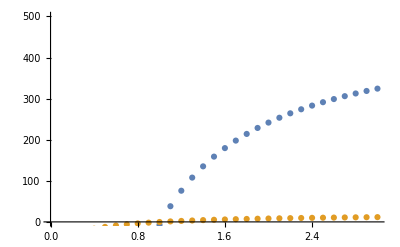

```mathematica
(* holding β2 at 0 *)
soltab = Table[{i,i11+i12,i22+i21}/.NSolve[sistar/.movSols/.sispars/.movpars/.β1->i/.β2->0,{i11,i12,i22,i21}][[2]],{i,.1,3,.1}];
ListPlot[{soltab[[;;,{1,2}]],soltab[[;;,{1,3}]]},PlotRange->{0,500}]
```

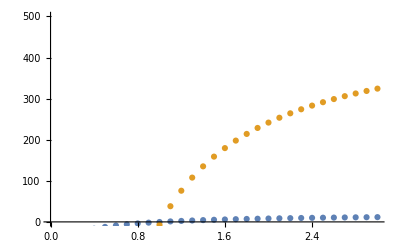

```mathematica
(* holding β1 at 0 *)
soltab = Table[{i,i11+i12,i22+i21}/.NSolve[sistar/.movSols/.sispars/.movpars/.β1->0/.β2->i,{i11,i12,i22,i21}][[2]],{i,.1,3,.1}];
ListPlot[{soltab[[;;,{1,2}]],soltab[[;;,{1,3}]]},PlotRange->{0,500}]
```

#### Second: check the zero travel case

```mathematica
movpars = {ϕ1->0.,  τ12 ->0.,ϕ2->0.,τ21 ->0.};
poppars = {n1->500.,n2->500.};
sispars = {γ->1.};
movSols ={n11->n1,n12->0,n22->n2,n21->0};
```

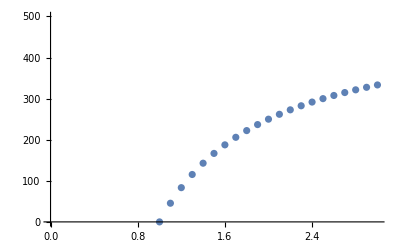

-Graphics-

```mathematica
soltab = Table[{i,i11+i12,i22+i21}/.NSolve[sistar/.movSols/.movpars/.sispars/.poppars/.β1->i/.β2->i,{i11,i12,i22,i21}][[1]],{i,.1,3,.1}];
ListPlot[soltab[[;;,{1,2}]],PlotRange->{0,500}]
ListPlot[soltab[[;;,{1,3}]],PlotRange->{0,500}]
```

```mathematica
594 + 135/3
```

639

## Flux Model

```mathematica
(* The TaR movement model *)
movflux ={0 == - f1 n1 + f2 n2,
(* Normalize to the total population *)
n ==n1+n2
};
(* The transmission model *)
sisflux ={
0 == β1  i1/n1(n1 - i1) - γ i1 - f1 i1 + f2 i2,
0 == β2  i2/n2(n2 - i2) - γ i2 -f2 i2+ f1 i1
};
```

### Flux Model Checks

#### First : check symmetry of equations

```mathematica
movpars = {f1->1/100., f2->1/100.};
poppars = {n->1000};
sispars = {γ->1.};
movSols =Flatten[Solve[movflux/.movpars/.poppars,{n1,n2}]//Chop];
```

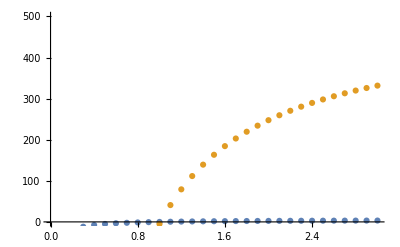

```mathematica
soltab = Table[{i,i1,i2}/.NSolve[sisflux/.movpars/.sispars/.movSols/.β1->0/.β2->i,{i1,i2}][[1]],{i,.1,3,.1}];
ListPlot[{soltab[[;;,{1,2}]],soltab[[;;,{1,3}]]},PlotRange->{0,500}]
```

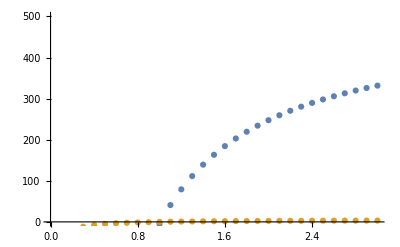

```mathematica
soltab = Table[{i,i1,i2}/.NSolve[sisflux/.movpars/.sispars/.movSols/.β1->i/.β2->0,{i1,i2}][[1]],{i,.1,3,.1}];
ListPlot[{soltab[[;;,{1,2}]],soltab[[;;,{1,3}]]},PlotRange->{0,500}]
```

#### Second : check zero travel case

```mathematica
movpars = {f1->0, f2->0};
poppars = {n->1000};
sispars = {γ->1.};
movSols ={n1->500.,n2->500.};
```

```mathematica
soltab = Table[{i,i1,i2}/.NSolve[sisflux/.movpars/.sispars/.movSols/.β1->i/.β2->i,{i1,i2}][[1]],{i,.1,3,.1}];
ListPlot[soltab[[;;,{1,2}]],PlotRange->{0,500}]
ListPlot[soltab[[;;,{1,3}]],PlotRange->{0,500}]
```

-Graphics-

-Graphics-

## Results: Matching Flux

The purpose of this exercise will be to match the flux from the TaR model to the flux from the flux model. To do this, I will need a way to generate movflux parameters from movtar parameters:

```mathematica
mtar ={m12-> (τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2,m21->(τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2};
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar
```

{f1→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n1,f2→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n2}

In all test cases, the first step will be to calculate the surfaces of i1 and i2 vs. β1 and β2 in the TaR model, then calculate the same surfaces for the comparable flux model:

#### Symmetric population and symmetric travel case “Boring Example”

The flux volumes between the two populations should be equal

```mathematica
tarpars= {ϕ1->1/5., τ12 ->1/3.,ϕ2->1/5.,τ21 ->1/3.};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]]
```

{n11→312.5,n12→187.5,n22→312.5,n21→187.5}

```mathematica
tarPRs =Flatten[Table[{i,j,i11+i12,i22+i21}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->j},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}],{i,.1,3,.1},{j,.1,3,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[tarPRs[[;;,{1,2,3}]],PlotRange->{0,500},AxesLabel->{"β1","β2","I1"}]
```

-Graphics3D-

```mathematica
ListPlot3D[tarPRs[[;;,{1,2,4}]],PlotRange->{0,500},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

```mathematica
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

```mathematica
fluxPRs = Flatten[Table[{i,j,i1,i2}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->j},{i1,240,0,500},{i2,240,0,500}],{i,.1,3,.1},{j,.1,3,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[fluxPRs[[;;,{1,2,3}]],PlotRange->{0,500},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

```mathematica
ListPlot3D[fluxPRs[[;;,{1,2,4}]],PlotRange->{0,500},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

```mathematica
(* Plotting the two sets of results together, we start to see discrepancies: *)
ListPlot3D[{tarPRs[[;;,{1,2,3}]],fluxPRs[[;;,{1,2,3}]]},PlotRange->{0,500},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

Plot some cross sections of these surfaces:

β2 =0.5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.01}];
```

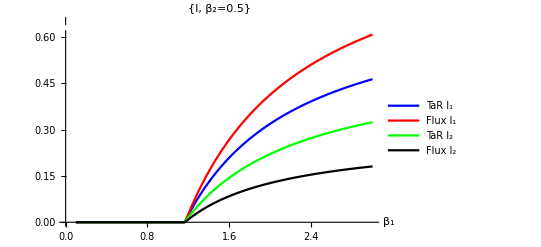

```mathematica
(* Making a Figure: *)
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I"},
PlotLabel->{"I, β_2=0.5"}]
Export["/Users/dtcitron/Documents/Movement_Models/Figures/Figure_4a_Symmetric-B1_05.png",%]
```

β2 = 2

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->2},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->2},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

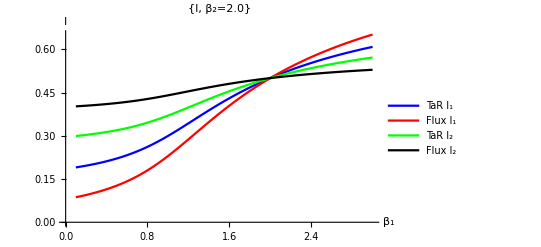

```mathematica
(* Making a Figure: *)
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I"},
PlotLabel->{"I, β_2=2.0"}]
Export["/Users/dtcitron/Documents/Movement_Models/Figures/Figure_4b_Symmetric-B1_2.png",%]
```

The extreme case where all travel backwards and forwards is the same:
What we end up seeing is that the TaR model creates a situation where there is effectively full mixing, and the two populations have equal prevalence even when β1 and β2 are different.
On the other hand, the flux model somehow accentuates the differences between the two populations when β1 and β2 are different.

```mathematica
tarpars= {ϕ1->1/3., τ12 ->1/3.,ϕ2->1/3.,τ21 ->1/3.};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]]
```

{n11→250.,n12→250.,n22→250.,n21→250.}

```mathematica
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

β2 =0.5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

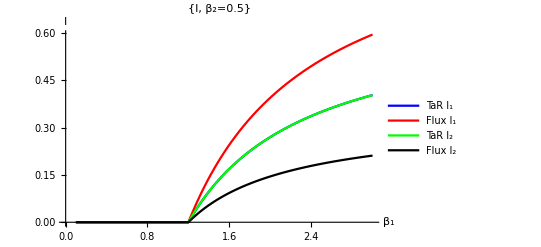

```mathematica
(* Making a Figure: *)
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I"},
PlotLabel->{"I, β_2=0.5"}]
Export["/Users/dtcitron/Documents/Movement_Models/Figures/Figure_5a_Symmetric-B2_05.png",%]
```

β2 = 2

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->2},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->2},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(* Making a Figure: *)
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I"},
PlotLabel->{"I, β_2=2.0"}]
Export["/Users/dtcitron/Documents/Movement_Models/Figures/Figure_5b_Symmetric-B2_2.png",%]
```

-Graphics-

/Users/dtcitron/Documents/Movement_Models/Figures/Figure_5b_Symmetric-B2_2.png

#### Asymmetric population; symmetric travel case

```mathematica
tarpars= {ϕ1->1/5., τ12 ->1/3.,ϕ2->1/5.,τ21 ->1/3.};
poppars={n1->1000.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.movpars/.poppars/.tarpars,{n11,n12,n22,n21}]]
```

{n11→625.,n12→375.,n22→312.5,n21→187.5}

```mathematica
tarPRs =Flatten[Table[{i,j,i11+i12,i22+i21}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1},{j,.1,3,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[tarPRs[[;;,{1,2,3}]],PlotRange->{0,1000},AxesLabel->{"β1","β2","I1"}]
```

-Graphics3D-

```mathematica
ListPlot3D[tarPRs[[;;,{1,2,4}]],PlotRange->{0,500},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

```mathematica
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movTarSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

```mathematica
fluxPRs = Flatten[Table[{i,j,i1,i2}/.FindRoot[sisflux/.fluxpars/.sispars/.movTarSols/.{β1->i,β2->j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1},{j,.1,3,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[fluxPRs[[;;,{1,2,3}]],PlotRange->{0,1000},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

```mathematica
ListPlot3D[fluxPRs[[;;,{1,2,4}]],PlotRange->{0,500},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

```mathematica
(* Plotting the two sets of results together, we start to see discrepancies: *)
ListPlot3D[{tarPRs[[;;,{1,2,3}]],fluxPRs[[;;,{1,2,3}]]},PlotRange->{0,750},AxesLabel->{"β1","β2","I1"}]
```

-Graphics3D-

```mathematica
(* Plotting the two sets of results together, we start to see discrepancies: *)
ListPlot3D[{tarPRs[[;;,{1,2,4}]],fluxPRs[[;;,{1,2,4}]]},PlotRange->{0,750},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

#### Asymmetric travel case, symmetric populations

The flux rates between the two places are no longer equal: people in location 1 travel very frequently but the people in location travel hardly travel at all

```mathematica
tarpars= {ϕ1->1/10.,τ12 ->1/3.,ϕ2->1/500.,τ21 ->1/3.};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.poppars/.tarpars,{n11,n12,n22,n21}]]
```

{n11→384.615,n12→115.385,n22→497.018,n21→2.98211}

```mathematica
tarPRs =Flatten[Table[{i,j,i11+i12,i22+i21}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1},{j,.1,3,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[tarPRs[[;;,{1,2,3}]],PlotRange->{0,500},AxesLabel->{"β1","β2","I1"}]
```

-Graphics3D-

```mathematica
ListPlot3D[tarPRs[[;;,{1,2,4}]],PlotRange->{0,500},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

```mathematica
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

```mathematica
fluxPRs = Flatten[Table[{i,j,i1,i2}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1},{j,.1,3,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[fluxPRs[[;;,{1,2,3}]],PlotRange->{0,500},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

```mathematica
ListPlot3D[fluxPRs[[;;,{1,2,4}]],PlotRange->{0,500},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

```mathematica
(* Plotting the two sets of results together, we start to see discrepancies: *)
ListPlot3D[{tarPRs[[;;,{1,2,3}]],fluxPRs[[;;,{1,2,3}]]},PlotRange->{0,500},AxesLabel->{"β1","β2","I1"}]
```

-Graphics3D-

```mathematica
(* Plotting the two sets of results together, we start to see discrepancies: *)
ListPlot3D[{tarPRs[[;;,{1,2,4}]],fluxPRs[[;;,{1,2,4}]]},PlotRange->{0,500},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

#### β2 = .75

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->.75},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1}];
```

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->.75},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1}];
```

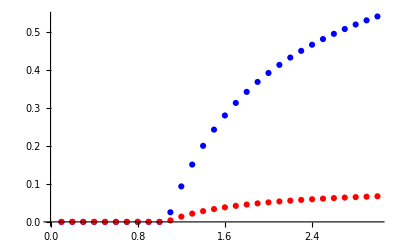

```mathematica
ListPlot[{tarPRSlices[[;;,{1,2}]],tarPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red}]
```

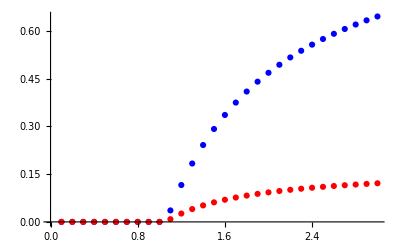

```mathematica
ListPlot[{fluxPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red}]
```

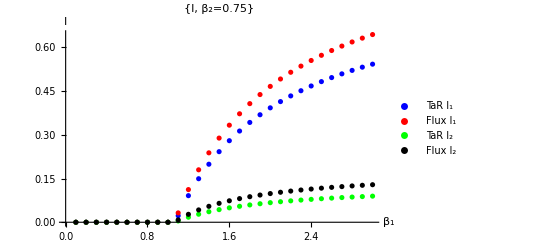

```mathematica
(* Making a Figure 1a: *)
ListPlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I"},
PlotLabel->{"I, β_2=0.75"}]
```

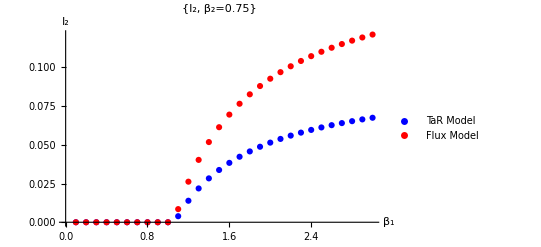

```mathematica
(* Figure 1b *) 
ListPlot[{tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red},
PlotLegends->{"TaR Model","Flux Model"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=0.75"}]
```

#### β2 = 2

```mathematica
tarPRSlices =Flatten[Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->2.},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1},{j,.1,3,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->2.},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

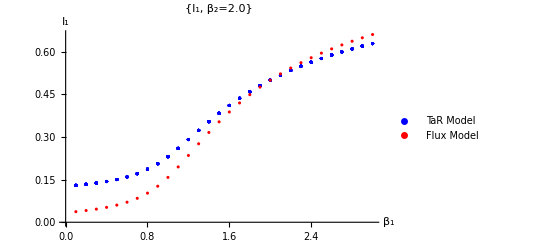

```mathematica
ListPlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]]},PlotStyle->{Blue,Red},
PlotLegends->{"TaR Model","Flux Model"},
AxesLabel->{"β_1","I_1"},
PlotLabel->{"I_1, β_2=2.0"}]
```

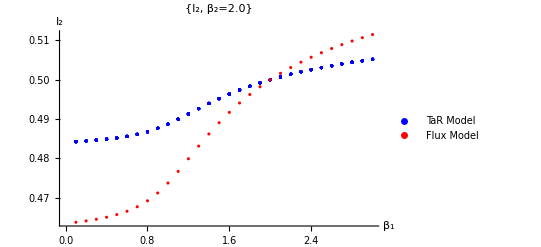

```mathematica
ListPlot[{tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red},
PlotLegends->{"TaR Model","Flux Model"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.0"}]
```

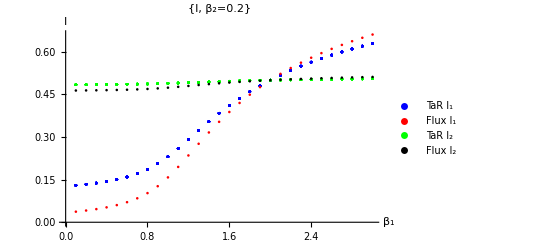

```mathematica
(* Making a Figure 1b: *)
ListPlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I"},
PlotLabel->{"I, β_2=0.2"}]
```

#### β2 = 3

```mathematica
tarPRSlices =Flatten[Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->3},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1},{j,.1,3,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->3},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

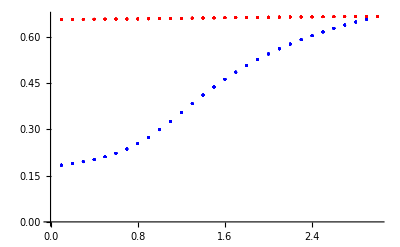

```mathematica
ListPlot[{tarPRSlices[[;;,{1,2}]],tarPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red}]
```

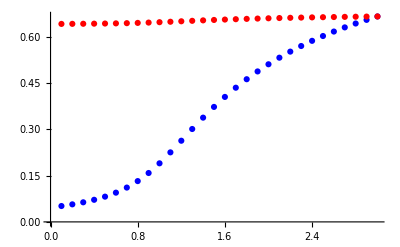

```mathematica
ListPlot[{fluxPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red}]
```

#### “Bioko Island”

Have patch 1 be the island; smaller population, frequent travel, low beta;
Have patch 2 be the mainland; larger population, no travel, very high beta;

```mathematica
poppars={n1->250.,n2->750.};
sispars={γ->1.};
tarpars = {ϕ1->1/210.,τ12->1/14,ϕ2->0,τ21->1/14};
movTarSols =Flatten[NSolve[movtar/.poppars/.tarpars,{n11,n12,n22,n21}]]
```

{n11→234.375,n12→15.625,n22→750.,n21→0.}

```mathematica
tarPRs =Flatten[Table[{i,j,i11+i12,i22+i21}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1},{j,.1,3,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.{n->(n1+n2)/.poppars},{n1,n2}]];
```

```mathematica
{1/f1, 1/f2}/.fluxpars
```

{224.,672.}

```mathematica
fluxPRs = Flatten[Table[{i,j,i1,i2}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1},{j,.1,3,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[{Table[Flatten[{tarPRs[[i,{1,2}]], tarPRs[[i,3]]/n1/.poppars}],{i,1,Length[tarPRs]}],Table[Flatten[{fluxPRs[[i,{1,2}]], fluxPRs[[i,3]]/n1/.poppars}],{i,1,Length[tarPRs]}]},
PlotRange->{0,1},AxesLabel->{"β1","β2","I1"}]
```

-Graphics3D-

```mathematica
ListPlot3D[{Table[Flatten[{tarPRs[[i,{1,2}]], tarPRs[[i,4]]/n2/.poppars}],{i,1,Length[tarPRs]}],Table[Flatten[{fluxPRs[[i,{1,2}]], fluxPRs[[i,4]]/n2/.poppars}],{i,1,Length[tarPRs]}]},
PlotRange->{0,1},AxesLabel->{"β1","β2","I1"}]
```

-Graphics3D-

For the Bioko Island example, we pick β2 = 5., which in a world without travel would create a prevalence on the mainland of 0.8.  This is a very high transmission setting.  Looking at the output as a function of

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->5.},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.01}];
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->5.},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Comparing the island prevalence as a function of β1, for both models - 
Flux model in Red, TaR model in Blue
We see that the critical point appears to be different for the two models, with the TaR model always being able to sustain transmission on the Island but the Flux model only for large enough β1 values.
In fact, using the flux model instead of the TaR model consistently overpredicts what β1 needs to be to sustain any level of transmission.

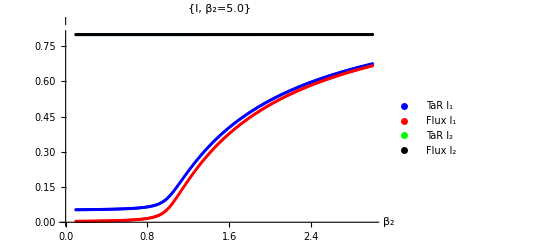

```mathematica
(* Use this to make figure 1 in the RMD notebook *)
ListPlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},
PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_2","I"},
PlotLabel->{"I, β_2=5.0"}]
```

#### “Forest Exposure”

Bulk of the population lives in location 1.
Population 2 doesn’t move
High transmission in location 2, very low transmission in location 1

```mathematica
tarpars= {ϕ1->1/60.,τ12 ->1/3.,ϕ2->0,τ21 ->1/3.};
poppars={n1->10000.,n2->100.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.poppars/.tarpars,{n11,n12,n22,n21}]]
```

{n11→9523.81,n12→476.19,n22→100.,n21→0.}

```mathematica
tarPRs =Flatten[Table[{i,j,i11+i12,i22+i21}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1},{j,.1,3,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.{n->(n1+n2)/.poppars},{n1,n2}]];
```

```mathematica
fluxPRs = Flatten[Table[{i,j,i1,i2}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.1},{j,.1,3,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[{Table[Flatten[{tarPRs[[i,{1,2}]], tarPRs[[i,3]]/n1/.poppars}],{i,1,Length[tarPRs]}],Table[Flatten[{fluxPRs[[i,{1,2}]], fluxPRs[[i,3]]/n1/.poppars}],{i,1,Length[tarPRs]}]},
PlotRange->{0,.1},
PlotLegends->{"TaR Surface", "Flux Surface"},AxesLabel->{"β_1","β_2","I_2"}]
```

-Graphics3D-

```mathematica
ListPlot3D[{Table[Flatten[{tarPRs[[i,{1,2}]], tarPRs[[i,4]]/n2/.poppars}],{i,1,Length[tarPRs]}],Table[Flatten[{fluxPRs[[i,{1,2}]], fluxPRs[[i,4]]/n2/.poppars}],{i,1,Length[tarPRs]}]},
PlotStyle->{Orange, LightBlue},
PlotLegends->{"TaR Surface", "Flux Surface"},
PlotRange->{0,1},AxesLabel->{"β_1","β_2","I_2"}]
```

-Graphics3D-

Taking a slice at constant β_1=0.5:

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->0.5,β2->i},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,5,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->0.5,β2->i},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,5,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

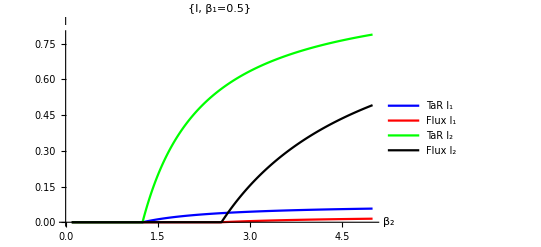

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},
PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_2","I"},
PlotLabel->{"I, β_1=0.5"}]
```

Taking a slice at constant β_1=1.5:

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->1.5,β2->i},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,5,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->1.5,β2->i},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,5,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

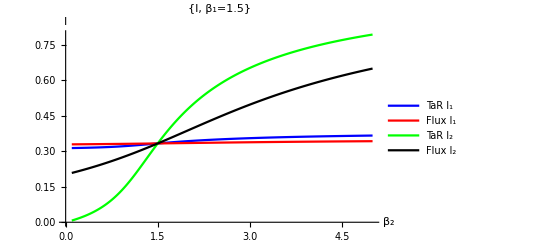

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},
PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_2","I"},
PlotLabel->{"I, β_1=1.5"}]
```

# Exploring Parameter Space

What are the dimensions that we care about, that are relevant to affecting transmission?
1. β_i - transmission rate
2. ϕ_ij- travel rate
3. τ_ij-  travel duration
4. N_i - baseline populations
Note how many time scales are included in the first 3 items alone!  All of them are of course relative to γ, the rate of recovery.  At base we can restrain τ_ij< ϕ_ij, ensuring that mostly people just spend their time at home.

We can imagine several different regimes:
1. β_1=β_2, β_1<β_2, β_1>β_2
2. τ_ij > γ (likely to recover while traveling), τ_ij < γ (unlikely to recover while traveling)
And then we vary ϕ_ijaccordingly
Note that this ignores the case of assigning very different travel times, eg τ_12>> τ_21- adding that flexibility makes it possible for τ_12> γ but τ_21< γ. 
For now, let’s just set γ = 1 and compute the 6 different scenarios where we’ve fixed τ_12= τ_21for simplicity.

## Define the model

```mathematica
(* The TaR movement model *)
movtar ={0 == - ϕ1 n11 + τ12 n12,
0 == - ϕ2 n22+ τ21  n21,
(* Normalize to the residence populations *)
n11 + n12 == n1,
n22 + n21 == n2
};
(* The transmission model *)
sistar ={(* On-diagonal terms *)
0 == β1(i11 + i21)/(n11+n21)(n11 - i11) - γ i11 - ϕ1 i11 + τ12 i12,
0 == β2(i22 + i12)/(n22 + n12)(n22 - i22) - γ i22 - ϕ2 i22 + τ21 i21,
(* Off-diagonal terms *)
0 == β2(i22 + i12)/(n22 + n12)(n12 - i12) - γ i12 + ϕ1 i11 - τ12 i12,
0 == β1 (i11 + i21)/(n11 + n21)(n21 - i21) - γ i21 + ϕ2 i22 - τ21 i21
};
```

```mathematica
(* The Flux movement model *)
movflux ={0 == - f1 n1 + f2 n2,
(* Normalize to the total population *)
n ==n1+n2
};
(* The transmission model *)
sisflux ={
0 == β1  i1/n1(n1 - i1) - γ i1 - f1 i1 + f2 i2,
0 == β2  i2/n2(n2 - i2) - γ i2 -f2 i2+ f1 i1
};
```

```mathematica
mtar ={m12-> (τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2,m21->(τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2};
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar
```

{f1→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n1,f2→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n2}

## β1 = β2 > γ, N1 = N2 (very boring)

This case turns out to be pretty boring!
In fact, it doesn’t really seem to matter at all what the different values of τ are - as long as β1 = β2, we end up with the same fractions of people sick in both populations

### τ12 = τ21 > γ

Equal transmission rates, but people return before recovering

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->2.};
poppars={n1->500.,n2->500.};
sispars={β1->1.5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}]
{i11+i12,i22+i21}/.%
```

{i11→162.602,i12→4.06504,i22→162.602,i21→4.06504}

{166.667,166.667}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}]
{i11+i12,i22+i21}/.%
```

{i11→111.111,i12→55.5556,i22→165.837,i21→0.829187}

{166.667,166.667}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{i1→166.667,i2→166.667}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{i1→166.667,i2→166.667}

```mathematica
(* Just to drive home how this regime doesn't really matter *)
```

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,i11+i12,i22+i21}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1,i2}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,400},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,400},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 = τ21 < γ

Equal transmission rates, but people recover before returning home
No difference from the above results!

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->.2};
poppars={n1->500.,n2->500.};
sispars={β1->1.5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}]
{i11+i12,i22+i21}/.%
```

{i11→133.333,i12→33.3333,i22→133.333,i21→33.3333}

{166.667,166.667}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}]
{i11+i12,i22+i21}/.%
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{i11→27.7778,i12→138.889,i22→158.73,i21→7.93651}

{166.667,166.667}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
```

{i1→166.667,i2→166.667}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
```

{i1→166.667,i2→166.667}

```mathematica
(* Just to drive home how this regime doesn't really matter *)
```

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,i11+i12,i22+i21}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1,i2}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,400},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,400},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

## β1 > β2 > γ; N1 = N2

Asymmetric infections

### τ12 = τ21 > γ

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->2.};
poppars={n1->500.,n2->500.};
sispars={β1->5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→388.705,i12→7.38362,i22→180.749,i21→8.24247}

{0.792178,0.377983}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→252.453,i12→99.4337,i22→202.514,i21→1.68602}

{0.703773,0.408401}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
```

{i1→395.152,i2→198.79}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
```

{i1→379.514,i2→264.607}

```mathematica
(* Note that here we do have separation of time spent traveling - so we do see a difference in how the two models predict exposure/prevalence in the end *)
```

```mathematica
(* Just to drive home how this regime doesn't really matter *)
```

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,i11+i12,i22+i21}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1,i2}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
(* Patch 1 is where β1 > β2, so I'd expect there to be less (?) infection in location 2 as the rate of movement ϕ1 increases *)
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{250,400},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
(* Patch 1 is where β1 > β2, so I'd expect there to be more infection in location 2 as the rate of movement ϕ2 increases *)
ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{250,400},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 = τ21 < γ

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->.2};
poppars={n1->500.,n2->500.};
sispars={β1->5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}]
{i11+i12,i22+i21}/.%
```

{i11→317.835,i12→41.536,i22→152.039,i21→78.2197}

{359.371,230.259}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}]
{i11+i12,i22+i21}/.%
```

{i11→59.8067,i12→169.436,i22→176.097,i21→18.2745}

{229.242,194.371}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
```

{i1→395.927,i2→194.33}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
```

{i1→392.044,i2→215.019}

```mathematica
(* Note that here we do have separation of time spent traveling - so we do see a difference in how the two models predict exposure/prevalence in the end *)
```

```mathematica
(* Just to drive home how this regime doesn't really matter *)
```

```mathematica
tarPRs=Flatten[Table[{i,j,i11+i12,i22+i21}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{i,j,i1,i2}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,450},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,450},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 > γ > τ21

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->.2};
poppars={n1->500.,n2->500.};
sispars={β1->5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}]
{i11+i12,i22+i21}/.%
```

{i11→388.78,i12→7.40518,i22→151.883,i21→78.27}

{396.185,230.153}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}]
{i11+i12,i22+i21}/.%
```

{i11→252.683,i12→99.5972,i22→195.033,i21→18.4814}

{352.281,213.515}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
```

{i1→395.535,i2→196.609}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
```

{i1→379.521,i2→264.583}

```mathematica
(* Note that here we do have separation of time spent traveling - so we do see a difference in how the two models predict exposure/prevalence in the end *)
```

```mathematica
(* Just to drive home how this regime doesn't really matter *)
```

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,i11+i12,i22+i21}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1,i2}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{250,400},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{250,400},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 < γ < τ21

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->2.};
poppars={n1->500.,n2->500.};
sispars={β1->5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}]
{i11+i12,i22+i21}/.%
```

{i11→317.706,i12→41.1031,i22→181.379,i21→8.23806}

{358.809,189.617}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}]
{i11+i12,i22+i21}/.%
```

{i11→59.4103,i12→168.731,i22→182.944,i21→1.62833}

{228.142,184.572}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
```

{i1→395.535,i2→196.609}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
```

{i1→392.029,i2→215.094}

```mathematica
(* Note that here we do have separation of time spent traveling - so we do see a difference in how the two models predict exposure/prevalence in the end *)
```

```mathematica
(* Just to drive home how this regime doesn't really matter *)
```

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,i11+i12,i22+i21}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,250,0,500},{i12,250,0,500},{i22,250,0,500},{i21,250,0,500}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1,i2}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{200,400},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{200,400},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

## β1 > β2 > γ; N1 > N2

Asymmetric infections, asymmetric populations -  the larger population is exposed to the higher transmission

### τ12 = τ21 > γ

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->2.};
poppars={n1->5000.,n2->500.};
sispars={β1->5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→3891.15,i12→75.4273,i22→201.766,i21→8.40282}

{0.793315,0.420338}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→2541.66,i12→1032.63,i22→233.101,i21→1.73426}

{0.714858,0.46967}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3981.49,i2→260.831}

{0.796299,0.521662}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3945.96,i2→362.659}

{0.789192,0.725317}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 = τ21 < γ

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->.2};
poppars={n1->5000.,n2->500.};
sispars={β1->5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→3181.47,i12→432.811,i22→160.076,i21→78.3599}

{0.722856,0.476872}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→598.397,i12→1758.6,i22→184.771,i21→18.2387}

{0.4714,0.406018}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3983.82,i2→251.929}

{0.796765,0.503857}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3965.05,i2→313.839}

{0.793011,0.627678}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.12,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 > γ > τ21

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->.2};
poppars={n1->5000.,n2->500.};
sispars={β1->5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→3891.31,i12→75.7216,i22→169.651,i21→78.5019}

{0.793407,0.496305}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./80},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→2542.1,i12→1033.27,i22→221.31,i21→22.9242}

{0.715075,0.488469}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3981.7,i2→260.08}

{0.796339,0.520159}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3945.96,i2→362.657}

{0.789192,0.725314}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 < γ < τ21

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->2.};
poppars={n1->5000.,n2->500.};
sispars={β1->5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→3181.31,i12→430.659,i22→192.547,i21→8.33014}

{0.722393,0.401755}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→597.916,i12→1757.33,i22→192.585,i21→1.64695}

{0.471049,0.388465}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3983.6,i2→252.801}

{0.79672,0.505601}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3965.05,i2→313.85}

{0.79301,0.6277}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.15,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

## β1 > β2 > γ; N2 > N1

Asymmetric infections - the smaller population is exposed to the higher transmission

### τ12 = τ21 > γ

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->2.};
poppars={n1->500.,n2->5000.};
sispars={β1->5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* These examples are not too far apart *)
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→385.867,i12→7.31654,i22→1767.75,i21→81.3328}

{0.786367,0.369816}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→250.484,i12→96.1753,i22→1753.71,i21→16.3865}

{0.693319,0.354019}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→372.94,i2→1848.64}

{0.745879,0.369727}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→363.434,i2→1899.83}

{0.726868,0.379966}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 = τ21 < γ

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->.2};
poppars={n1->500.,n2->5000.};
sispars={β1->5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→317.109,i12→40.7787,i22→1485.97,i21→780.072}

{0.715775,0.453208}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→60.1941,i12→161.924,i22→1655.65,i21→184.298}

{0.444236,0.36799}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→377.267,i2→1823.45}

{0.754533,0.36469}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→385.823,i2→1769.7}

{0.771645,0.353939}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 > γ > τ21

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->.2};
poppars={n1->500.,n2->5000.};
sispars={β1->5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→387.83,i12→7.36261,i22→1485.05,i21→780.383}

{0.790386,0.453087}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./80},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→252.139,i12→96.7845,i22→1679.53,i21→228.082}

{0.697848,0.381523}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→376.865,i2→1825.84}

{0.753729,0.365169}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→363.601,i2→1898.98}

{0.727203,0.379795}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.12,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 < γ < τ21

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->2.};
poppars={n1->500.,n2->5000.};
sispars={β1->5,β2->1.5,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→314.961,i12→40.2587,i22→1768.62,i21→81.1191}

{0.710439,0.369948}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./90},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{i11→58.5882,i12→160.451,i22→1717.85,i21→17.7174}

{0.438078,0.347113}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→373.325,i2→1846.45}

{0.746649,0.369289}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→385.608,i2→1771.11}

{0.771217,0.354222}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

## β1 > γ > β2 ; N1 = N2

Asymmetric infections - let the high transmission patch drive transmission in the low transmission patch

### τ12 = τ21 > γ

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->2.};
poppars={n1->500.,n2->500.};
sispars={β1->5,β2->.75,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→388.088,i12→6.62153,i22→48.4192,i21→7.282}

{0.78942,0.111402}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→247.044,i12→87.3884,i22→81.5193,i21→1.49547}

{0.668865,0.166029}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→392.27,i2→81.4673}

{0.78454,0.162935}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→369.522,i2→203.07}

{0.739043,0.406141}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 = τ21 < γ

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->.2};
poppars={n1->500.,n2->500.};
sispars={β1->5,β2->.75,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{i11→316.592,i12→20.1545,i22→49.6123,i21→77.1236}

{0.673493,0.253472}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→55.2975,i12→75.3786,i22→47.2552,i21→17.7104}

{0.261352,0.129931}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→393.462,i2→71.8918}

{0.786923,0.143784}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→387.576,i2→114.27}

{0.775151,0.22854}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 > γ > τ21

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->.2};
poppars={n1->500.,n2->500.};
sispars={β1->5,β2->.75,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{i11→388.204,i12→6.65405,i22→48.0894,i21→77.2052}

{0.789717,0.250589}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→247.388,i12→87.6281,i22→80.4222,i21→18.1632}

{0.670032,0.197171}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→392.858,i2→76.8218}

{0.785716,0.153644}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→369.532,i2→203.029}

{0.739065,0.406057}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 < γ < τ21

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->2.};
poppars={n1->500.,n2->500.};
sispars={β1->5,β2->.75,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→316.367,i12→19.2373,i22→51.2771,i21→7.28293}

{0.671208,0.11712}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→54.3755,i12→73.5293,i22→46.7483,i21→1.36791}

{0.25581,0.0962323}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→392.858,i2→76.8218}

{0.785716,0.153644}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→387.553,i2→114.416}

{0.775105,0.228832}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

## β1 > γ > β2 ; N1 > N2

Asymmetric infections - let the high transmission patch drive transmission in the low transmission patch

### τ12 = τ21 > γ

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->2.};
poppars={n1->5000.,n2->500.};
sispars={β1->5,β2->.75,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→3887.36,i12→68.2187,i22→87.4469,i21→7.58163}

{0.791115,0.190057}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→2492.97,i12→921.89,i22→134.669,i21→1.58001}

{0.682971,0.272498}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3972.95,i2→197.009}

{0.79459,0.394017}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3930.32,i2→352.012}

{0.786064,0.704024}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 = τ21 < γ

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->.2};
poppars={n1->5000.,n2->500.};
sispars={β1->5,β2->.75,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→3171.37,i12→234.931,i22→66.0228,i21→77.3923}

{0.68126,0.28683}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→553.851,i12→879.858,i22→65.5845,i21→17.6523}

{0.286742,0.166474}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3976.11,i2→181.743}

{0.795222,0.363487}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3951.98,i2→281.984}

{0.790396,0.563968}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::reged: The point {1870.94,5000.,142.107,287.755} is at the edge of the search region {0.,5000.} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {1873.13,5000.,140.556,287.07} is at the edge of the search region {0.,5000.} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {1875.34,5000.,139.387,286.373} is at the edge of the search region {0.,5000.} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 > γ > τ21

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->.2};
poppars={n1->5000.,n2->500.};
sispars={β1->5,β2->.75,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→3887.56,i12→68.5857,i22→79.8069,i21→77.6158}

{0.79123,0.314845}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→2493.46,i12→922.523,i22→129.911,i21→18.2898}

{0.683197,0.296403}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3973.22,i2→195.733}

{0.794644,0.391465}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3930.32,i2→352.01}

{0.786064,0.70402}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 < γ < τ21

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->2.};
poppars={n1->5000.,n2->500.};
sispars={β1->5,β2->.75,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→3171.08,i12→230.92,i22→74.864,i21→7.47718}

{0.6804,0.164682}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→552.763,i12→876.953,i22→67.4593,i21→1.41267}

{0.285943,0.137744}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3975.81,i2→183.253}

{0.795161,0.366507}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→3951.98,i2→282.001}

{0.790395,0.564002}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.145,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

## β1 > γ > β2 ; N2 > N1

Asymmetric infections - let the high transmission patch drive transmission in the low transmission patch

### τ12 = τ21 > γ

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->2.};
poppars={n1->500.,n2->5000.};
sispars={β1->5,β2->.75,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→383.149,i12→6.50419,i22→400.358,i21→70.4861}

{0.779307,0.0941689}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→243.77,i12→82.6671,i22→262.682,i21→13.9624}

{0.652874,0.0553288}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→353.941,i2→501.301}

{0.707883,0.10026}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→337.389,i2→616.748}

{0.674777,0.12335}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 = τ21 < γ

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->.2};
poppars={n1->500.,n2->5000.};
sispars={β1->5,β2->.75,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→315.329,i12→18.5739,i22→419.305,i21→767.288}

{0.667805,0.237319}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→55.99,i12→58.3492,i22→211.99,i21→179.845}

{0.228678,0.0783669}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→361.375,i2→441.419}

{0.722749,0.0882838}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→375.939,i2→305.73}

{0.751879,0.061146}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 > γ > τ21

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->2.,τ21 ->.2};
poppars={n1->500.,n2->5000.};
sispars={β1->5,β2->.75,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→386.578,i12→6.59046,i22→415.758,i21→767.856}

{0.786337,0.236723}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→246.287,i12→83.6423,i22→283.58,i21→180.798}

{0.659859,0.0928754}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→360.686,i2→447.203}

{0.721372,0.0894406}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→337.683,i2→614.885}

{0.675366,0.122977}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.05},{j,.1,1,.05}],1];
```

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

### τ12 < γ < τ21

```mathematica
(* Define the TaR model parameters *)
tarpars= {τ12 ->.2,τ21 ->2.};
poppars={n1->500.,n2->5000.};
sispars={β1->5,β2->.75,γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
```

```mathematica
(* Define the Flux model parameters *)
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->((n1+n2)/.poppars),{n1,n2}]];
```

```mathematica
(* Two numerical examples: TaR model *)
```

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./20,ϕ2->1./20},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→311.454,i12→17.3455,i22→403.59,i21→70.0025}

{0.6576,0.0947185}

```mathematica
FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./1,ϕ2->1./100},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}]
{(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.%
```

{i11→52.095,i12→53.1418,i22→177.746,i21→12.7241}

{0.210474,0.0380941}

```mathematica
(* Two numerical examples: Flux model *)
```

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./20,ϕ2->1./20},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→354.605,i2→496.179}

{0.70921,0.0992357}

```mathematica
FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./1,ϕ2->1./100},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}]
{i1/n1/.poppars/.%,i2/n2/.poppars/.%}
```

{i1→375.576,i2→309.46}

{0.751152,0.0618921}

```mathematica
tarPRs=Flatten[Table[{1./i,1./j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{ϕ1->1./i,ϕ2->1./j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.12,1,.1},{j,.1,1,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
fluxPRs = Flatten[Table[{1./i,1./j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{ϕ1->1./i,ϕ2->1./j},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,1,.1},{j,.1,1,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[{fluxPRs[[;;,{1,2,3}]],tarPRs[[;;,{1,2,3}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]

ListPlot3D[{fluxPRs[[;;,{1,2,4}]],tarPRs[[;;,{1,2,4}]]},PlotRange->{0,1},AxesLabel->{"ϕ1","ϕ2","I1"},PlotStyle->{Blue, Orange}]
```

-Graphics3D-

-Graphics3D-

# Mean-Field TaR matrix

## TaR Model

```mathematica
(* The TaR movement model *)
movtar ={0 == - ϕ1 n11 + τ12 n12,
0 == - ϕ2 n22+ τ21  n21,
(* Normalize to the residence populations *)
n11 + n12 == n1,
n22 + n21 == n2
};
(* The transmission model *)
sistar ={(* On-diagonal terms *)
0 == β1(i11 + i21)/(n11+n21)(n11 - i11) - γ i11 - ϕ1 i11 + τ12 i12,
0 == β2(i22 + i12)/(n22 + n12)(n22 - i22) - γ i22 - ϕ2 i22 + τ21 i21,
(* Off-diagonal terms *)
0 == β2(i22 + i12)/(n22 + n12)(n12 - i12) - γ i12 + ϕ1 i11 - τ12 i12,
0 == β1 (i11 + i21)/(n11 + n21)(n21 - i21) - γ i21 + ϕ2 i22 - τ21 i21
};
```

```mathematica
(* Define the Time at Risk matrix for the TaR model: *)
movTarSols =Flatten[Solve[movtar,{n11,n12,n22,n21}]]
```

{n11→(n1 τ12)/(τ12+ϕ1),n12→(n1 ϕ1)/(τ12+ϕ1),n22→(n2 τ21)/(τ21+ϕ2),n21→(n2 ϕ2)/(τ21+ϕ2)}

```mathematica
tarPsi = {{n11/n1, n12/n1},{n21/n2,n22/n2}}/.movTarSols
```

{{τ12/(τ12+ϕ1),ϕ1/(τ12+ϕ1)},{ϕ2/(τ21+ϕ2),τ21/(τ21+ϕ2)}}

And now we define the SIS model.  This is similar to how it is defined in Cosner et al., but different from how it appears in Ruktanonchai et al.  The difference comes from how the force of infection doesn’t account for how people move around here - I_i/N_i rather than ψ^T I/ψ^TN

```mathematica
tarTarPsiEqs = tarPsi.{β1 i1/n1,β2 i2/n2}*{(n1-i1),(n2-i2)} -γ {i1,i2}
```

{-i1 γ+(-i1+n1) ((i1 β1 τ12)/(n1 (τ12+ϕ1))+(i2 β2 ϕ1)/(n2 (τ12+ϕ1))),-i2 γ+(-i2+n2) ((i2 β2 τ21)/(n2 (τ21+ϕ2))+(i1 β1 ϕ2)/(n1 (τ21+ϕ2)))}

#### A check on the equations:

What solutions do we get when β2 = 0?

```mathematica
tarTarPsiEqs/.β2->0
```

{-i1 γ+(i1 (-i1+n1) β1 τ12)/(n1 (τ12+ϕ1)),-i2 γ+(i1 (-i2+n2) β1 ϕ2)/(n1 (τ21+ϕ2))}

## 2-patch R0 comparison with full TaR model

```mathematica
JacMF = {{D[tarTarPsiEqs[[1]],i1],D[tarTarPsiEqs[[1]],i2]},{D[tarTarPsiEqs[[2]],i1],D[tarTarPsiEqs[[2]],i2]}};
JacMF//MatrixForm
```

(-γ-(i1 β1 τ12)/(n1 (τ12+ϕ1))+((-i1+n1) β1 τ12)/(n1 (τ12+ϕ1))-(i2 β2 ϕ1)/(n2 (τ12+ϕ1)) | ((-i1+n1) β2 ϕ1)/(n2 (τ12+ϕ1))
((-i2+n2) β1 ϕ2)/(n1 (τ21+ϕ2)) | -γ-(i2 β2 τ21)/(n2 (τ21+ϕ2))+((-i2+n2) β2 τ21)/(n2 (τ21+ϕ2))-(i1 β1 ϕ2)/(n1 (τ21+ϕ2)))

```mathematica
JacMF/.{i1->0,i2->0}//MatrixForm
```

(-γ+(β1 τ12)/(τ12+ϕ1) | (n1 β2 ϕ1)/(n2 (τ12+ϕ1))
(n2 β1 ϕ2)/(n1 (τ21+ϕ2)) | -γ+(β2 τ21)/(τ21+ϕ2))

```mathematica
tarpars= {ϕ1->1/180., τ12 ->1/14.,ϕ2->1/180.,τ21 ->1/14.};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
Eigensystem[JacMF/.{i1->0,i2->0}/.tarpars/.poppars/.sispars]
```

{{-0.5 (2.-0.927835 β1-0.927835 β2+1. √(0.860878 β1^2-1.70092 β1 β2+0.860878 β2^2)),0.5 (-2.+0.927835 β1+0.927835 β2+1. √(0.860878 β1^2-1.70092 β1 β2+0.860878 β2^2))},{{(6.42857 (0.+1. β1-1. β2-1.07778 √(0.860878 β1^2-1.70092 β1 β2+0.860878 β2^2)))/β1,1.},{(6.42857 (0.+1. β1-1. β2+1.07778 √(0.860878 β1^2-1.70092 β1 β2+0.860878 β2^2)))/β1,1.}}}

Here' s how to interpret what’s going on here:  We have found the Jacobian and set all I_ivalues to 0 to represent the no-infection state.  The largest eigenvalue determines whether or not this is stable: if the largest eigenvalue is positive, then a perturbation away form zero will result in exponential increase in the number of infected people - that is to say, the onset of endemic disease.
Below I am plotting the two eigenvalues as a function of transmission parameters [β1 and β2].  Blue shows the larger eigenvalue.  The points where the blue surface intersects with zero (in black) represent the critical points where the transmission parameters are large enough to hold the prevalence above zero.

```mathematica
Plot3D[{-0.5 (2.-0.9278350515463918 β1-0.9278350515463918 β2+1. √(0.8608778828780954 β1^2-1.7009246466149432 β1 β2+0.8608778828780954 β2^2)),0.5 (-2.+0.9278350515463918 β1+0.9278350515463918 β2+1. √(0.8608778828780954 β1^2-1.7009246466149432 β1 β2+0.8608778828780954 β2^2)),0},{β1,0,3},{β2,0,3},PlotRange->{-1,1},PlotStyle->{Yellow,Blue,Black}]
```

-Graphics3D-

```mathematica
(* Solve for the shape of that surface *) 
Solve[0==0.5 (-2.+0.9278350515463918 β1+0.9278350515463918 β2+1. √(0.8608778828780954 β1^2-1.7009246466149432 β1 β2+0.8608778828780954 β2^2)),β2]
```

{{β2→(-97.+90. β1)/(-90.+83. β1)}}

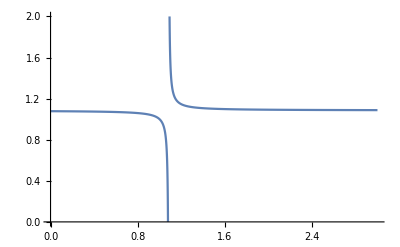

```mathematica
Plot[(-97.+90. β1)/(-90.+83. β1),{β1,0,3},PlotRange->{0,2}]
```

And comparing this to the SIS model with explicit movement

```mathematica
tarpars= {ϕ1->1/180., τ12 ->1/14.,ϕ2->1/180.,τ21 ->1/14.};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[Solve[movtar,{n11,n12,n22,n21}]]
sistarvars = {i11,i12,i21,i22};
jacTaR = Table[D[sistar[[j,2]]/.movTarSols/.tarpars/.poppars/.sispars,sistarvars[[k]]],{j,1,Length[sistar]},{k,1,Length[sistarvars]}];
```

{n11→(n1 τ12)/(τ12+ϕ1),n12→(n1 ϕ1)/(τ12+ϕ1),n22→(n2 τ21)/(τ21+ϕ2),n21→(n2 ϕ2)/(τ21+ϕ2)}

```mathematica
jacTaR//MatrixForm
```

(-1.00556+0.002 (463.918-i11) β1-0.002 (i11+i21) β1 | 0.0714286 | 0.002 (463.918-i11) β1 | 0
0 | 0.002 (463.918-i22) β2 | 0.0714286 | -1.00556+0.002 (463.918-i22) β2-0.002 (i12+i22) β2
0.00555556 | -1.07143+0.002 (36.0825-i12) β2-0.002 (i12+i22) β2 | 0 | 0.002 (36.0825-i12) β2
0.002 (36.0825-i21) β1 | 0 | -1.07143+0.002 (36.0825-i21) β1-0.002 (i11+i21) β1 | 0.00555556)

```mathematica
Eigenvalues[jacTaR/.{i11->0,i12->0,i21->0,i22->0}]
```

{Root[1.15989-1.14879 β1-1.14879 β2+1.13769 β1 β2-5.00745×10^-19 β1^2 β2^2+(1.23084-0.143545 β1-1.06509 β2+8.67362×10^-19 β1 β2) #1+(0.0709442-0.85567 β2+0.85567 β1 β2) #1^2+(1.-0.927835 β1-0.927835 β2) #1^3+1. #1^4&,1],Root[1.15989-1.14879 β1-1.14879 β2+1.13769 β1 β2-5.00745×10^-19 β1^2 β2^2+(1.23084-0.143545 β1-1.06509 β2+8.67362×10^-19 β1 β2) #1+(0.0709442-0.85567 β2+0.85567 β1 β2) #1^2+(1.-0.927835 β1-0.927835 β2) #1^3+1. #1^4&,2],Root[1.15989-1.14879 β1-1.14879 β2+1.13769 β1 β2-5.00745×10^-19 β1^2 β2^2+(1.23084-0.143545 β1-1.06509 β2+8.67362×10^-19 β1 β2) #1+(0.0709442-0.85567 β2+0.85567 β1 β2) #1^2+(1.-0.927835 β1-0.927835 β2) #1^3+1. #1^4&,3],Root[1.15989-1.14879 β1-1.14879 β2+1.13769 β1 β2-5.00745×10^-19 β1^2 β2^2+(1.23084-0.143545 β1-1.06509 β2+8.67362×10^-19 β1 β2) #1+(0.0709442-0.85567 β2+0.85567 β1 β2) #1^2+(1.-0.927835 β1-0.927835 β2) #1^3+1. #1^4&,4]}

```mathematica
Plot3D[{Root[1.159894809775762-1.1487918806315958 β1-1.1487918806315958 β2+1.1376889514874295 β1 β2-5.007449209005216*^-19 β1^2 β2^2+(1.2308390022675737-0.1435450125067209 β1-1.0650881314725202 β2+8.673617379884035*^-19 β1 β2) #1+(0.07094419249181153-0.8556701030927835 β2+0.8556701030927834 β1 β2) #1^2+(1.-0.9278350515463917 β1-0.9278350515463917 β2) #1^3+1. #1^4&,2],0},{β1,0,3},{β2,0,3}]
```

-Graphics3D-

Note that the critical point has moved - we have a different solution model from before, and this changes the Jacobian, the eigensystem, and the critical point.

## Example - Initial Exploration

```mathematica
tarpars1= {ϕ1->1/100., τ12 ->1/3.,ϕ2->1/500.,τ21 ->1/3.};
poppars={n1->500.,n2->500.};
sispars={γ->1};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]]
```

{n11→463.918,n12→36.0825,n22→463.918,n21→36.0825}

#### β2 = 0.75

```mathematica
(* Mean Field TaR model *)
tarPsiSlices =Table[{j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars1/.poppars/.sispars/.{β1->.075,β2 ->j},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{j,0,3,.05}];
(* Comparing the above result to the original full explicit movement model: *)
tarPRSlices=Table[{j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars2/.sispars/.movTarSols/.{β1->.075,β2 ->j}(*{β1->j,β2->0.75}*),{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{j,0,3,.05}];
```

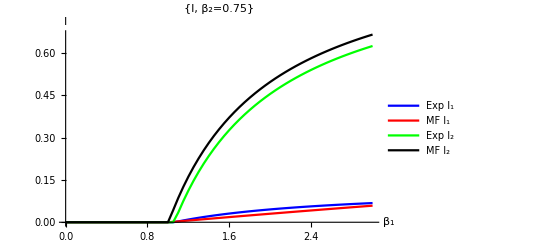

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],tarPsiSlices[[;;,{1,2}]],tarPRSlices[[;;,{1,3}]],tarPsiSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"Exp I_1","MF I_1","Exp I_2","MF I_2"},
AxesLabel->{"β_1","I"},
PlotLabel->{"I, β_2=0.75"}]
```

#### β2 = 2.0

```mathematica
(* Mean Field TaR model *)
tarPsiSlices =Table[{j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars1/.poppars/.sispars/.{β1->j,β2 ->2.},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{j,0,3,.05}];
(* Comparing the above result to the original full explicit movement model: *)
tarPRSlices=Table[{j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars2/.sispars/.movTarSols/.{β1->j,β2->2.},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{j,0,3,.05}];
```

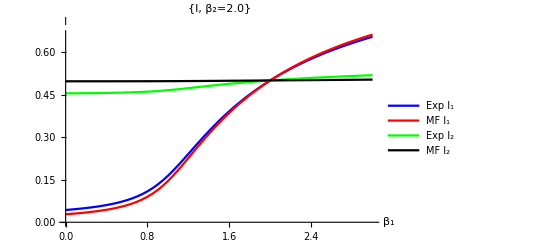

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],tarPsiSlices[[;;,{1,2}]],tarPRSlices[[;;,{1,3}]],tarPsiSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"Exp I_1","MF I_1","Exp I_2","MF I_2"},
AxesLabel->{"β_1","I"},
PlotLabel->{"I, β_2=2.0"}]
```

## Example - symmetric movement - “boring” example

```mathematica
tarpars1= {ϕ1->1/180., τ12 ->1/14.,ϕ2->1/180.,τ21 ->1/14.};
poppars={n1->500.,n2->500.};
sispars={γ->1};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]]
```

{n11→463.918,n12→36.0825,n22→463.918,n21→36.0825}

```mathematica
(* Mean Field TaR model *)
tarPsiSols = Flatten[Table[{j, k,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars1/.poppars/.sispars/.{β1->j,β2 ->k},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{j,0,3,.05},{k,0,3,.05}],1];
(* Comparing the above result to the original full explicit movement model: *)
tarPRs =Flatten[Table[{i,j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars2/.sispars/.movTarSols/.{β1->i,β2->j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,0,3,.05},{j,0,3,.05}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
(* Showing the differences between the two sets of solutions *)
ListPlot3D[{tarPRs[[;;,{1,2,3}]],tarPsiSols[[;;,{1,2,3}]]},
PlotStyle->{Blue, Yellow},AxesLabel->{"β1","β2","I1"}]
ListPlot3D[{tarPRs[[;;,{1,2,4}]],tarPsiSols[[;;,{1,2,4}]]},
PlotStyle->{Blue, Yellow},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* And the absolute differences between the surfaces *) ListPlot3D[Table[Flatten[{tarPRs[[i,{1,2}]],{tarPRs[[i,3]]-tarPsiSols[[i,3]]}}],{i,1,Length[tarPRs]}],AxesLabel->{"β1","β2","I1"}]
ListPlot3D[Table[Flatten[{tarPRs[[i,{1,2}]],{tarPRs[[i,4]]-tarPsiSols[[i,4]]}}],{i,1,Length[tarPRs]}],AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

-Graphics3D-

## Example - “Bioko Island” model

```mathematica
poppars={n1->250.,n2->750.};
sispars={γ->1.};
tarpars = {ϕ1->1/210.,τ12->1/14,ϕ2->0,τ21->1/14};
movTarSols =Flatten[NSolve[movtar/.poppars/.tarpars,{n11,n12,n22,n21}]]
```

{n11→234.375,n12→15.625,n22→750.,n21→0.}

```mathematica
(* Mean Field TaR model *)
tarPsiSols = Flatten[Table[{j, k,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars/.poppars/.sispars/.{β1->j,β2 ->k},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{j,0,6,.1},{k,0,6,.1}],1];
(* Comparing the above result to the original full explicit movement model: *)
tarPRs =Flatten[Table[{i,j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->j},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,0,6,.1},{j,0,6,.1}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
(* Showing the differences between the two sets of solutions *)
ListPlot3D[{tarPRs[[;;,{1,2,3}]],tarPsiSols[[;;,{1,2,3}]]},
PlotStyle->{Blue, Yellow},AxesLabel->{"β1","β2","I1"}]
ListPlot3D[{tarPRs[[;;,{1,2,4}]],tarPsiSols[[;;,{1,2,4}]]},
PlotStyle->{Blue, Yellow},AxesLabel->{"β1","β2","I2"}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* And the absolute differences between the surfaces *) ListPlot3D[Table[Flatten[{tarPRs[[i,{1,2}]],{tarPRs[[i,3]]-tarPsiSols[[i,3]]}}],{i,1,Length[tarPRs]}],AxesLabel->{"β1","β2","I1"}]
ListPlot3D[Table[Flatten[{tarPRs[[i,{1,2}]],{tarPRs[[i,4]]-tarPsiSols[[i,4]]}}],{i,1,Length[tarPRs]}],AxesLabel->{"β1","β2","I1"}]
```

-Graphics3D-

-Graphics3D-

#### β2 = 5

```mathematica
(* Mean Field TaR model *)
tarPsiSlices =Table[{j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars1/.poppars/.sispars/.{β1->j,β2 ->5.},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{j,0,3,.05}];
(* Comparing the above result to the original full explicit movement model: *)
tarPRSlices=Table[{j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars2/.sispars/.movTarSols/.{β1->j,β2 ->5.}(*{β1->j,β2->0.75}*),{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{j,0,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

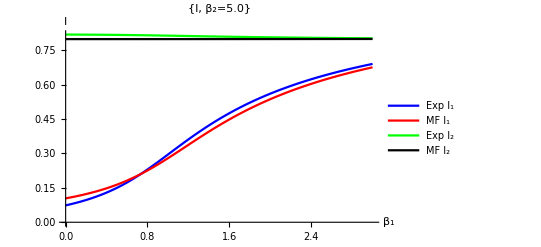

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],tarPsiSlices[[;;,{1,2}]],tarPRSlices[[;;,{1,3}]],tarPsiSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"Exp I_1","MF I_1","Exp I_2","MF I_2"},
AxesLabel->{"β_1","I"},
PlotLabel->{"I, β_2=5.0"}]
```

#### β2 = 5

```mathematica
(* Mean Field TaR model *)
tarPsiSlices =Table[{j,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars1/.poppars/.sispars/.{β1->j,β2 ->.75},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{j,0,3,.05}];
(* Comparing the above result to the original full explicit movement model: *)
tarPRSlices=Table[{j,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars2/.sispars/.movTarSols/.{β1->j,β2 ->.75},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{j,0,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

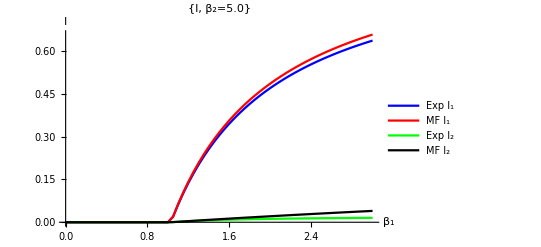

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],tarPsiSlices[[;;,{1,2}]],tarPRSlices[[;;,{1,3}]],tarPsiSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"Exp I_1","MF I_1","Exp I_2","MF I_2"},
AxesLabel->{"β_1","I"},
PlotLabel->{"I, β_2=5.0"}]
```

# Ross-Macdonald Model

Here we will illustrate an example, a two-patch model where the transmission in patch 2 is much higher and travel from patch 1 to patch 2 is more frequent than the reverse.
We will calculate R0 using both the Flux RM model and the TaR RM model, and show how the mapping between R0 and Prevalence is different for the two models.

```mathematica
rmPars = {
a -> 0.27,
b -> 0.55,
c -> 0.15,
r ->  1/200.,
g -> .9,
peip ->.9^11
};
pij = {{ψ11,ψ12},{ψ21,ψ22}};
fij = {{0,f1},{f2,0}}; (* we can calibrate the flux model to match the TaR model *)
Hvec = {H1,H2};
Xvec = {X1,X2};
Mvec = {M1,M2};
Zvec = {Z1,Z2};
```

```mathematica
(* The TaR movement model *)
movtar ={0 == - ϕ1 n11 + τ12 n12,
0 == - ϕ2 n22+ τ21  n21,
(* Normalize to the residence populations *)
n11 + n12 == n1,
n22 + n21 == n2
};
```

```mathematica
(* Ross-Macdonald model, adapted with TaR movement model *)
rmTarEqs = Flatten[Table[{0==Flatten[{b a(Hvec - Xvec)pij.(Zvec/(Transpose[pij].Hvec)) - r Xvec,a c ((Transpose[pij].Xvec)/(Transpose[pij].Hvec))(Mvec*peip - Zvec) - g Zvec}][[k]]},{k,1,4}]];
rmTarEqs//MatrixForm
```

(0==-r X1+a b (H1-X1) ((Z1 ψ11)/(H1 ψ11+H2 ψ21)+(Z2 ψ12)/(H1 ψ12+H2 ψ22))
0==-r X2+a b (H2-X2) ((Z1 ψ21)/(H1 ψ11+H2 ψ21)+(Z2 ψ22)/(H1 ψ12+H2 ψ22))
0==-g Z1+(a c (M1 peip-Z1) (X1 ψ11+X2 ψ21))/(H1 ψ11+H2 ψ21)
0==-g Z2+(a c (M2 peip-Z2) (X1 ψ12+X2 ψ22))/(H1 ψ12+H2 ψ22))

```mathematica
(* Ross-Macdonald model, adapted with Flux movement model *)
rmFluxEqs = 
Flatten[Table[0 == Flatten[{b a (Hvec - Xvec)(Zvec/Hvec)+Transpose[fij].Xvec - fij.{1,1}*Xvec-r Xvec,a c Xvec/Hvec(peip Mvec - Zvec) - g Zvec}][[k]],{k,1,4}]];
rmFluxEqs//MatrixForm
```

(0==-f1 X1-r X1+f2 X2+(a b (H1-X1) Z1)/H1
0==f1 X1-f2 X2-r X2+(a b (H2-X2) Z2)/H2
0==(a c X1 (M1 peip-Z1))/H1-g Z1
0==(a c X2 (M2 peip-Z2))/H2-g Z2)

```mathematica
(* Writing out ψ matrix *)
pij/.{ψ11-> n11/n1,ψ12-> n12/n1,ψ21-> n21/n2,ψ22-> n22/n2}/.Solve[movtar,{n11,n12,n22,n21}][[1]]
(* Writing out f matrix *)
mtar ={m12-> (τ12 ϕ1)/(τ12+ϕ1)H1+(τ21 ϕ2)/(τ21+ϕ2)H2,m21->(τ12 ϕ1)/(τ12+ϕ1)H1+(τ21 ϕ2)/(τ21+ϕ2)H2};
fluxpars ={f1->(m12/H1),f2->(m21/H2)}/.mtar;
fij/.fluxpars
```

{{τ12/(τ12+ϕ1),ϕ1/(τ12+ϕ1)},{ϕ2/(τ21+ϕ2),τ21/(τ21+ϕ2)}}

{{0,((H1 τ12 ϕ1)/(τ12+ϕ1)+(H2 τ21 ϕ2)/(τ21+ϕ2))/H1},{((H1 τ12 ϕ1)/(τ12+ϕ1)+(H2 τ21 ϕ2)/(τ21+ϕ2))/H2,0}}

### Symmetric travel, “boring” example

```mathematica
(* The parameters for the RM equations *)
poppars={H1->500.,H2->500.};
tarpars= {ϕ1->1/5., τ12 ->1/3.,ϕ2->1/5.,τ21 ->1/3.};
```

```mathematica
rmTarEqs/.{ψ11-> n11/n1,ψ12-> n12/n1,ψ21-> n21/n2,ψ22-> n22/n2}/.Solve[movtar,{n11,n12,n22,n21}][[1]]/.rmPars/.poppars/.tarpars
```

{0==-0.005 X1+0.1485 (500.-X1) (0.00125 Z1+0.00075 Z2),0==-0.005 X2+0.1485 (500.-X2) (0.00075 Z1+0.00125 Z2),0==0.000081 (0.625 X1+0.375 X2) (0.313811 M1-Z1)-0.9 Z1,0==0.000081 (0.375 X1+0.625 X2) (0.313811 M2-Z2)-0.9 Z2}

```mathematica
TaRSols =Flatten[Table[{j,k,X1,X2,Z1,Z2}/.FindRoot[rmTarEqs/.{ψ11-> n11/n1,ψ12-> n12/n1,ψ21-> n21/n2,ψ22-> n22/n2}/.Solve[movtar,{n11,n12,n22,n21}][[1]]/.rmPars/.poppars/.tarpars/.{M1->j,M2->k},
{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}],
{j,0,2500,125},{k,0,2500,125}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[TaRSols[[;;,{1,2,3}]],AxesLabel->{"β1","β2","X1"},PlotRange->{0,500}]
ListPlot3D[TaRSols[[;;,{1,2,4}]],AxesLabel->{"β1","β2","X2"},PlotRange->{0,500}]
```

-Graphics3D-

-Graphics3D-

```mathematica
ListPlot3D[Table[{TaRSols[[j,1]],TaRSols[[j,2]],TaRSols[[j,3]]-TaRSols[[j,4]]},{j,1,Length[TaRSols]}]]
```

-Graphics3D-

```mathematica
(* How big does M2 need to be to maintain 80% prevalence in area 2? *)
NSolve[.8*500 ==(a^2 b c H2 M2 peip-g H2^2 r)/(a c (a b M2 peip+H2 r))/.rmPars/.poppars,M2]
```

{{M2→6175.37}}

```mathematica
(* And holding M2 high enough to maintain close to 80% prevalence in area 2: *)
TaRSols =Table[{j,X1,X2,Z1,Z2}/.FindRoot[rmTarEqs/.{ψ11-> n11/n1,ψ12-> n12/n1,ψ21-> n21/n2,ψ22-> n22/n2}/.Solve[movtar,{n11,n12,n22,n21}][[1]]/.rmPars/.poppars/.tarpars/.{M1->j,M2->6175},
{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}],
{j,0,2500,250}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

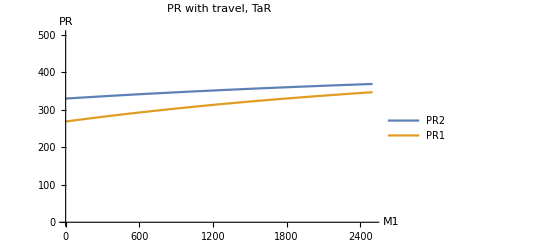

/Users/dtcitron/Documents/Movement_Models/Figures/Figure_8_RM-Boring-TaR.png

```mathematica
ListLinePlot[{TaRSols[[;;,{1,3}]],TaRSols[[;;,{1,2}]]}, AxesLabel->{"M1","PR"},PlotRange->{0,500},PlotLabel->"PR with travel, TaR",PlotLegends->{"PR2","PR1"}]
Export["/Users/dtcitron/Documents/Movement_Models/Figures/Figure_8_RM-Boring-TaR.png",%]
```

```mathematica
(* How much mosquito activity do I need to sustain PR of .2 in location 1? *)
NSolve[rmTarEqs/.{ψ11-> n11/n1,ψ12-> n12/n1,ψ21-> n21/n2,ψ22-> n22/n2}/.Solve[movtar,{n11,n12,n22,n21}][[1]]/.rmPars/.poppars/.tarpars/.{X1->.2*H1/.poppars,X2->.25*H2/.poppars},{M1,M2,Z1,Z2}]
```

{{M1→687.938,M2→2387.42,Z1→2.10438,Z2→7.71605}}

```mathematica
(* Show: what happens when we plug those numbers back in - do we get the right values of X1 and X2? *)FindRoot[rmTarEqs/.{ψ11-> n11/n1,ψ12-> n12/n1,ψ21-> n21/n2,ψ22-> n22/n2}/.Solve[movtar,{n11,n12,n22,n21}][[1]]/.rmPars/.poppars/.tarpars/.{M1->688,M2->2387},{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}]
```

{X1→99.9616,X2→124.951,Z1→2.10376,Z2→7.7117}

```mathematica
(* So it looks like M1 = 308, M2 = 9460 will be enough to sustain transmission close to 20% in area 1.  What happens when we take out travel? *)
FindRoot[Chop[rmTarEqs/.rmPars/.poppars/.{ψ12->0,ψ21->0}]/.{M1->688,M2->2387},{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}]
```

{X1→5.86915×10^-13,X2→244.78,Z1→1.17643×10^-14,Z2→16.1464}

```mathematica
(* What happens when we remove travel? *)
TaRSols =Table[{j,X1,X2,Z1,Z2}/.FindRoot[rmTarEqs/.{ψ11-> 1,ψ12-> 0,ψ21-> 0,ψ22-> 1}/.rmPars/.poppars/.tarpars/.{M1->j,M2->2387},
{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}],
{j,0,2500,250}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

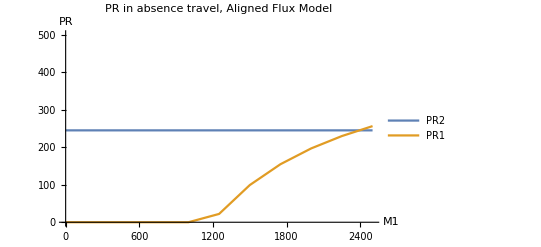

```mathematica
(*ListLinePlot[TaRSols[[;;,{1,2}]], AxesLabel->{"M1","PR1"},PlotRange->{0,500},PlotLabel->"PR1 in the absence of travel"]
ListLinePlot[TaRSols[[;;,{1,3}]], AxesLabel->{"M1","PR2"},PlotRange->{0,500}]*)
ListLinePlot[{TaRSols[[;;,{1,3}]],TaRSols[[;;,{1,2}]]}, AxesLabel->{"M1","PR"},PlotRange->{0,500},PlotLabel->"PR in absence travel, Aligned Flux Model",PlotLegends->{"PR2","PR1"}]
```

And now the comparison with the Flux model:

```mathematica
FindRoot[rmFluxEqs/.fluxpars/.rmPars/.poppars/.tarpars/.{M1->600,M2->2600},
{{X1,.9*H1/.poppars,0,H1/.poppars},
{X2,.9*H2/.poppars,0,H2/.poppars},
{Z1,10H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}]
```

{X1→123.469,X2→125.013,Z1→2.06928,Z2→9.07776}

```mathematica
FluxSols =Flatten[Table[{j,k,X1,X2,Z1,Z2}/.FindRoot[rmFluxEqs/.fluxpars/.rmPars/.poppars/.tarpars/.{M1->j,M2->k},
{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}],
{j,0,2500,125},{k,0,2500,125}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[FluxSols[[;;,{1,2,3}]],AxesLabel->{"β1","β2","X1"},PlotRange->{0,500}]
ListPlot3D[FluxSols[[;;,{1,2,4}]],AxesLabel->{"β1","β2","X2"},PlotRange->{0,500}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* Showing the differences between the two locations -
 note that the dynamic range is much smaller, meaning that there's less asymmetry in this model than in the TaR model.  The Flux model smooths out the differences between the two models. *) ListPlot3D[Table[{FluxSols[[j,1]],FluxSols[[j,2]],FluxSols[[j,3]]-FluxSols[[j,4]]},{j,1,Length[FluxSols]}]]
```

-Graphics3D-

```mathematica
(* Let's see what happens if we hold M2=2387, which was enough to hold prevalence in location 1 close to 20% in the TaR model *)
FluxSols =Table[{j,X1,X2,Z1,Z2}/.FindRoot[rmFluxEqs/.fluxpars/.rmPars/.poppars/.tarpars/.{M1->j,M2->2387},
{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}],
{j,0,2500,250}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(*ListLinePlot[FluxSols[[;;,{1,2}]], AxesLabel->{"M1","PR1"},PlotRange->{0,500},PlotLabel->"PR1 with travel, Aligned Flux Model"]
ListLinePlot[FluxSols[[;;,{1,3}]], AxesLabel->{"M1","PR2"},PlotRange->{0,500}]*)
```

One interesting difference between the Flux model and the TaR model is that there is some flexibility allowed regarding differences between PR in the two regions - here, for the TaR model, those differences are erased

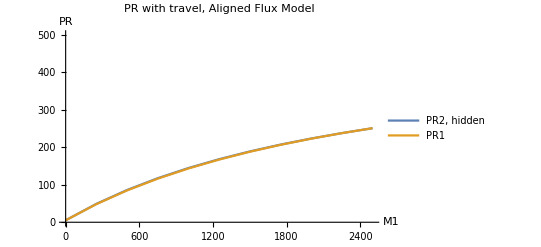

/Users/dtcitron/Documents/Movement_Models/Figures/Figure_8_RM-Borning-Flux.png

```mathematica
(* Kind of astonishing how close the two are - we are holding M2 constant! *)
ListLinePlot[{FluxSols[[;;,{1,3}]],FluxSols[[;;,{1,2}]]}, AxesLabel->{"M1","PR"},PlotRange->{0,500},PlotLabel->"PR with travel, Aligned Flux Model",PlotLegends->{"PR2, hidden","PR1"}]
Export["/Users/dtcitron/Documents/Movement_Models/Figures/Figure_8_RM-Boring-Flux.png",%]
```

```mathematica
(* And removing travel altogehter *)
FluxSols =Table[{j,X1,X2,Z1,Z2}/.FindRoot[rmFluxEqs/.{f1->0,f2->0}/.rmPars/.poppars/.tarpars/.{M1->j,M2->2387},
{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}],
{j,0,2500,250}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

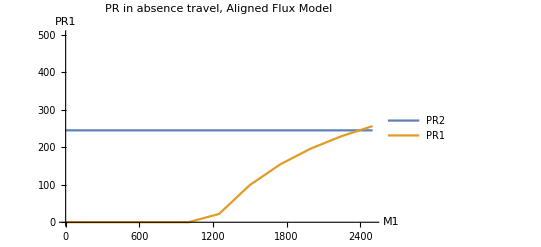

```mathematica
ListLinePlot[{FluxSols[[;;,{1,3}]],FluxSols[[;;,{1,2}]]}, AxesLabel->{"M1","PR1"},PlotRange->{0,500},PlotLabel->"PR in absence travel, Aligned Flux Model",PlotLegends->{"PR2","PR1"}]
```

### Asymmetric travel, Bioko - island - esque 2 - patch example

```mathematica
(* The parameters for the RM equations *)
poppars={H1->250.,H2->750.};
(*tarpars = {ϕ1->0.,τ12->1/14,ϕ2->0,τ21->1/14};*)
tarpars = {ϕ1->1/365.,τ12->1/14,ϕ2->0,τ21->1/14};
```

```mathematica
rmTarEqs/.{ψ11-> n11/n1,ψ12-> n12/n1,ψ21-> n21/n2,ψ22-> n22/n2}/.Solve[movtar,{n11,n12,n22,n21}][[1]]/.rmPars/.poppars/.tarpars
```

{0==-0.005 X1+0.1485 (250.-X1) (0.004 Z1+0.0000486533 Z2),0==-0.005 X2+0.1485 (750.-X2) (0.+0.00131712 Z2),0==0.000162 X1 (0.313811 M1-Z1)-0.9 Z1,0==0.0000533432 (0.0369393 X1+X2) (0.313811 M2-Z2)-0.9 Z2}

```mathematica
TaRSols =Flatten[Table[{j,k,X1,X2,Z1,Z2}/.FindRoot[rmTarEqs/.{ψ11-> n11/n1,ψ12-> n12/n1,ψ21-> n21/n2,ψ22-> n22/n2}/.Solve[movtar,{n11,n12,n22,n21}][[1]]/.rmPars/.poppars/.tarpars/.{M1->j,M2->k},
{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}],
{j,0,2500,250},{k,0,15000,1500}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[TaRSols[[;;,{1,2,3}]],AxesLabel->{"β1","β2","X1"},PlotRange->{0,250}]
ListPlot3D[TaRSols[[;;,{1,2,4}]],AxesLabel->{"β1","β2","X2"},PlotRange->{0,750}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* How big does M2 need to be to maintain 80% prevalence in area 2? *)
NSolve[.8*750 ==(a^2 b c H2 M2 peip-g H2^2 r)/(a c (a b M2 peip+H2 r))/.rmPars/.poppars,M2]
```

{{M2→9263.06}}

```mathematica
(* And holding M2 high enough to maintain close to 80% prevalence in area 2: *)
TaRSols =Table[{j,X1,X2,Z1,Z2}/.FindRoot[rmTarEqs/.{ψ11-> n11/n1,ψ12-> n12/n1,ψ21-> n21/n2,ψ22-> n22/n2}/.Solve[movtar,{n11,n12,n22,n21}][[1]]/.rmPars/.poppars/.tarpars/.{M1->j,M2->9250},
{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}],
{j,0,2500,250}];
```

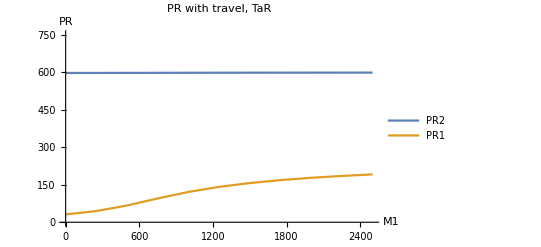

/Users/dtcitron/Documents/Movement_Models/Figures/Figure_9_RM-BI-TaR.png

```mathematica
(*ListLinePlot[TaRSols[[;;,{1,2}]], AxesLabel->{"M1","PR1"},PlotRange->{0,.8*250},PlotLabel->"PR1 with travel"]
ListLinePlot[TaRSols[[;;,{1,3}]], AxesLabel->{"M1","PR2"},PlotRange->{0,.8*750}]*)
ListLinePlot[{TaRSols[[;;,{1,3}]],TaRSols[[;;,{1,2}]]}, AxesLabel->{"M1","PR"},PlotRange->{0,750},PlotLabel->"PR with travel, TaR",PlotLegends->{"PR2","PR1"}]
Export["/Users/dtcitron/Documents/Movement_Models/Figures/Figure_9_RM-BI-TaR.png",%]
```

```mathematica
(* How much mosquito activity do I need to sustain PR of .2 in location 1? *)
NSolve[rmTarEqs/.{ψ11-> n11/n1,ψ12-> n12/n1,ψ21-> n21/n2,ψ22-> n22/n2}/.Solve[movtar,{n11,n12,n22,n21}][[1]]/.rmPars/.poppars/.tarpars/.{X1->.2*H1/.poppars,X2->.8*H2/.poppars},{M1,M2,Z1,Z2}]
```

{{M1→307.466,M2→9460.45,Z1→0.860629,Z2→102.254}}

```mathematica
(* Show: what happens when we plug those numbers back in - do we get the right values of X1 and X2? *)FindRoot[rmTarEqs/.{ψ11-> n11/n1,ψ12-> n12/n1,ψ21-> n21/n2,ψ22-> n22/n2}/.Solve[movtar,{n11,n12,n22,n21}][[1]]/.rmPars/.poppars/.tarpars/.{M1->308,M2->9460},{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}]
```

{X1→50.0401,X2→599.993,Z1→0.862809,Z2→102.248}

```mathematica
(* So it looks like M1 = 308, M2 = 9460 will be enough to sustain transmission close to 20% in area 1.  What happens when we take out travel? *)
FindRoot[Chop[rmTarEqs/.rmPars/.poppars/.{ψ12->0,ψ21->0}]/.{M1->308,M2->9460},{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{X1→1.97215×10^-31,X2→603.096,Z1→0.,Z2→103.671}

```mathematica
(* What happens when we remove travel? *)
TaRSolsNT =Table[{j,X1,X2,Z1,Z2}/.FindRoot[rmTarEqs/.{ψ11-> 1,ψ12-> 0,ψ21-> 0,ψ22-> 1}/.rmPars/.poppars/.tarpars/.{M1->j,M2->9460},
{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}],
{j,0,2500,250}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

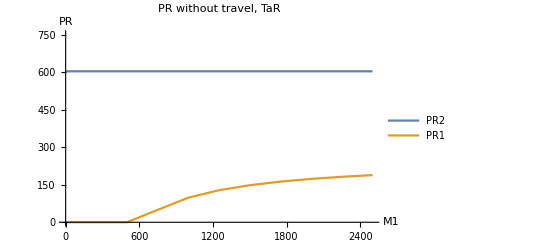

```mathematica
(*ListLinePlot[TaRSols[[;;,{1,2}]], AxesLabel->{"M1","PR1"},PlotRange->{0,.8*250},PlotLabel->"PR1 in the absence of travel"]
ListLinePlot[TaRSols[[;;,{1,3}]], AxesLabel->{"M1","PR2"},PlotRange->{0,750}]*)
ListLinePlot[{TaRSolsNT[[;;,{1,3}]],TaRSolsNT[[;;,{1,2}]]}, AxesLabel->{"M1","PR"},PlotRange->{0,750},PlotLabel->"PR without travel, TaR",PlotLegends->{"PR2","PR1"}]
```

And now the comparison with the Flux model:

```mathematica
FindRoot[rmFluxEqs/.fluxpars/.rmPars/.poppars/.tarpars/.{M1->1000,M2->9000},
{{X1,.9*H1/.poppars,0,H1/.poppars},
{X2,.9*H2/.poppars,0,H2/.poppars},
{Z1,10H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}]
```

{X1→134.258,X2→587.207,Z1→7.40475,Z2→96.1202}

```mathematica
FluxSols =Flatten[Table[{j,k,X1,X2,Z1,Z2}/.FindRoot[rmFluxEqs/.fluxpars/.rmPars/.poppars/.tarpars/.{M1->j,M2->k},
{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}],
{j,0,2500,250},{k,0,15000,1500}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[FluxSols[[;;,{1,2,3}]],AxesLabel->{"β1","β2","X1"},PlotRange->{0,250}]
ListPlot3D[FluxSols[[;;,{1,2,4}]],AxesLabel->{"β1","β2","X2"},PlotRange->{0,750}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* Let's see what happens if we hold M2=9250, which was enough to hold prevalence in location 1 close to 20% in the TaR model *)
FluxSols =Table[{j,X1,X2,Z1,Z2}/.FindRoot[rmFluxEqs/.fluxpars/.rmPars/.poppars/.tarpars/.{M1->j,M2->9460},
{{X1,.99*H1/.poppars,0,H1/.poppars},
{X2,.99*H2/.poppars,0,H2/.poppars},
{Z1,9H1/.poppars,0,1000*9H1/.poppars},
{Z2,9H2/.poppars,0,1000*9H2/.poppars}}],
{j,0,2500,250}];
```

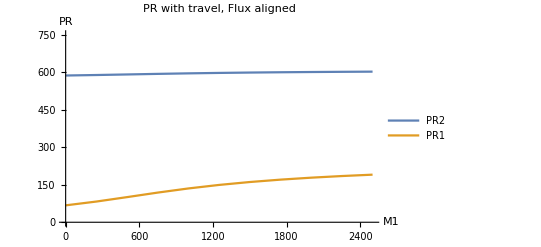

/Users/dtcitron/Documents/Movement_Models/Figures/Figure_9_RM-BI-Flux.png

```mathematica
(*ListLinePlot[FluxSols[[;;,{1,2}]], AxesLabel->{"M1","PR1"},PlotRange->{0,.8*250},PlotLabel->"PR with travel, Aligned Flux Model"]
ListLinePlot[FluxSols[[;;,{1,3}]], AxesLabel->{"M1","PR2"},PlotRange->{0,750}]*)
ListLinePlot[{FluxSols[[;;,{1,3}]],FluxSols[[;;,{1,2}]]}, AxesLabel->{"M1","PR"},PlotRange->{0,750},PlotLabel->"PR with travel, Flux aligned",PlotLegends->{"PR2","PR1"}]
Export["/Users/dtcitron/Documents/Movement_Models/Figures/Figure_9_RM-BI-Flux.png",%]
```

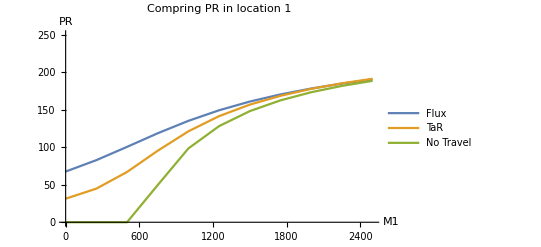

/Users/dtcitron/Documents/Movement_Models/Figures/Figure_9_RM-BI-NT.png

```mathematica
(*Show what happens in the absence of travel:*)
ListLinePlot[{FluxSols[[;;,{1,2}]],TaRSols[[;;,{1,2}]],TaRSolsNT[[;;,{1,2}]]}, AxesLabel->{"M1","PR"},PlotRange->{0,250},PlotLabel->"Compring PR in location 1",PlotLegends->{"Flux","TaR","No Travel"}]
Export["/Users/dtcitron/Documents/Movement_Models/Figures/Figure_9_RM-BI-NT.png",%]
```

```mathematica
(* If we take out travel, it'll be identical to the TaR model without travel *)
(* What if we solve for the amount of mosquito activity we need to sustain a PR of .2 in location 1? 
Note that fewer mosquitoes are needed ehre than in the TaR model 
I suppose the real revelation here is that there is no solution - the surface of solutions does not permit PR of 0.2 in location 1 and PR of 0.8 in location 2 *)
NSolve[rmFluxEqs/.fluxpars/.rmPars/.poppars/.tarpars/.{X1->.2*H1/.poppars,X2->.8 H2/.poppars},{M1,M2,Z1,Z2}]
```

{{M1→-438.387,M2→10485.1,Z1→-1.22709,Z2→114.336}}

# Suggested fix

How do we get around the fundamental limitations of flux data?  All flux data tells us is the number/fraction of people moving from one place to another.  It erases the details of how frequently each person moves between locations.

One thing we can do, though, is assume that the number of visitors returning home is small compared to the number of people who are leaving.  This overestimates the rates at which people leave, but if we combine it with assumptions/data about visiting times we can still approximate the rates at which people return home.

(Dave’s other idea: assume that the fraction of people who are visiting i from j is the same as the fraction of people visiting j from i?)

```mathematica
(* The TaR movement model *)
movtar ={0 == - ϕ1 n11 + τ12 n12,
0 == - ϕ2 n22+ τ21  n21,
(* Normalize to the residence populations *)
n11 + n12 == n1,
n22 + n21 == n2
};
(* Define the Time at Risk matrix for the TaR model: *)
movTarSols =Flatten[Solve[movtar,{n11,n12,n22,n21}]]
```

{n11→(n1 τ12)/(τ12+ϕ1),n12→(n1 ϕ1)/(τ12+ϕ1),n22→(n2 τ21)/(τ21+ϕ2),n21→(n2 ϕ2)/(τ21+ϕ2)}

```mathematica
tarPsi = {{n11/n1, n12/n1},{n21/n2,n22/n2}}/.movTarSols
```

{{τ12/(τ12+ϕ1),ϕ1/(τ12+ϕ1)},{ϕ2/(τ21+ϕ2),τ21/(τ21+ϕ2)}}

```mathematica
(* The TaR movement model *)
movflux ={0 == - f1 n1 + f2 n2,
(* Normalize to the total population *)
n ==n1+n2
};

mtar ={m12-> (τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2,m21->(τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2};
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar
```

{f1→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n1,f2→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n2}

How well does this perform?   Suppose I know τij for sure:

```mathematica
n12/.movTarSols
```

(n1 ϕ1)/(τ12+ϕ1)

```mathematica
mapprox ={mx12 ->  (τ12 ϕ1)/(τ12+ϕ1)n1, mx21->(τ21 ϕ2)/(τ21+ϕ2)n2}
```

{mx12→(n1 τ12 ϕ1)/(τ12+ϕ1),mx21→(n2 τ21 ϕ2)/(τ21+ϕ2)}

```mathematica
mx12/τ12/.mapprox
```

(n1 ϕ1)/(τ12+ϕ1)

```mathematica
(* SIS Bioko island example *)
poppars={n1->250.,n2->750.};
sispars={γ->1.};
tarpars = {ϕ1->1/210.,τ12->1/14,ϕ2->0,τ21->1/14};
movTarSols =Flatten[NSolve[movtar/.poppars/.tarpars,{n11,n12,n22,n21}]]
```

{n11→234.375,n12→15.625,n22→750.,n21→0.}

```mathematica
m12/(1/14)/.mtar/.poppars/.tarpars
m21/(1/14)/.mtar/.poppars/.tarpars
```

15.625

15.625

```mathematica
(* in this case we get n12 exactly right, but n21 completely wrong, on account of zero travel *)
```

```mathematica
(* SIS Bioko island example *)
poppars={n1->250.,n2->750.};
sispars={γ->1.};
tarpars = {ϕ1->1/210.,τ12->1/14,ϕ2->1/100,τ21->1/14};
movTarSols =Flatten[NSolve[movtar/.poppars/.tarpars,{n11,n12,n22,n21}]]

m12/(1/14)/.mtar/.poppars/.tarpars
m21/(1/14)/.mtar/.poppars/.tarpars
```

{n11→234.375,n12→15.625,n22→657.895,n21→92.1053}

107.73

107.73

```mathematica
(* Again, for this kind of asymmetry, we get it super wrong *)
```

```mathematica
(* SIS symmetric popualtions *)
poppars={n1->250.,n2->250.};
sispars={γ->1.};
tarpars = {ϕ1->1/100.,τ12->1/14,ϕ2->1/100,τ21->1/14};
movTarSols =Flatten[NSolve[movtar/.poppars/.tarpars,{n11,n12,n22,n21}]]

m12/τ12/.mtar/.poppars/.tarpars
m21/τ21/.mtar/.poppars/.tarpars
```

{n11→219.298,n12→30.7018,n22→219.298,n21→30.7018}

61.4035

61.4035

Try this now for 3 patches, just to make sure:

```mathematica
movtar ={
(* n1  *)
0==-ϕ1(π12+π13) n11+τ12 n12+τ13 n13,
0 == ϕ1 π12 n11 - τ12 n12,
0 == ϕ1 π13 n11 - τ13 n13,
(* n2 *)
0==-ϕ2(π21+π23) n22+τ21 n21+τ23 n23,
0 == ϕ2 π21 n22 - τ21 n21,
0 == ϕ2 π23 n22 - τ23 n23,
(* n3 *)
0==-ϕ3(π31+π32) n33+τ31 n31+τ32 n32,
0 == ϕ3 π31 n33 - τ31 n31,
0 == ϕ3 π32 n33 - τ32 n32,
(* Normalize to the residence populations *)
n11+n12+n13==n1,
n22+n21+n23==n2,
n33+n31+n32==n3
};
movflux ={
0==-f12 n1-f13 n1+f21 n2+f31 n3,
0==-f21 n2-f23 n2+f12 n1+f32 n3,
0== -f31 n3 - f32 n3 + f13 n1 + f23 n2,
(* Normalize to the total population *)
n ==n1+n2 + n3
};
```

```mathematica
movTarSols =Flatten[Solve[movtar,{n11,n12,n13, n21,n22,n23, n31,n32,n33}]]
```

{n11→(n1 τ12 τ13)/(τ12 τ13+π13 τ12 ϕ1+π12 τ13 ϕ1),n12→(n1 π12 τ13 ϕ1)/(τ12 τ13+π13 τ12 ϕ1+π12 τ13 ϕ1),n13→(n1 π13 τ12 ϕ1)/(τ12 τ13+π13 τ12 ϕ1+π12 τ13 ϕ1),n21→(n2 π21 τ23 ϕ2)/(τ21 τ23+π23 τ21 ϕ2+π21 τ23 ϕ2),n22→(n2 τ21 τ23)/(τ21 τ23+π23 τ21 ϕ2+π21 τ23 ϕ2),n23→(n2 π23 τ21 ϕ2)/(τ21 τ23+π23 τ21 ϕ2+π21 τ23 ϕ2),n31→(n3 π31 τ32 ϕ3)/(τ31 τ32+π32 τ31 ϕ3+π31 τ32 ϕ3),n32→(n3 π32 τ31 ϕ3)/(τ31 τ32+π32 τ31 ϕ3+π31 τ32 ϕ3),n33→(n3 τ31 τ32)/(τ31 τ32+π32 τ31 ϕ3+π31 τ32 ϕ3)}

```mathematica
mtar = {
m12 -> ϕ1 π12 n11 + τ21 n21,
m13 -> ϕ1 π13 n11 + τ31 n31,
m21 -> ϕ2 π21 n22 + τ12 n12,
m23 -> ϕ2 π23 n22 + τ32 n32,
m31 -> ϕ3 π31 n33 + τ13 n13,
m32 -> ϕ3 π32 n33 + τ23 n23
}
```

{m12→n21 τ21+n11 π12 ϕ1,m13→n31 τ31+n11 π13 ϕ1,m21→n12 τ12+n22 π21 ϕ2,m23→n32 τ32+n22 π23 ϕ2,m31→n13 τ13+n33 π31 ϕ3,m32→n23 τ23+n33 π32 ϕ3}

```mathematica
(* SIS symmetric popualtions *)
poppars={n1->250.,n2->250.,n3->250};
sispars={γ->1.};
tarpars = {
ϕ1->1/100.,π12 -> 1/2, π13->1/2,τ12->1/14,τ13->1/14,
ϕ2->1/500.,π21->1/5, π23->4/5,τ21->1/14,τ23->1/14,
ϕ3->1/100., π31->0, π32->1,τ31->1/14, τ32->1/14};
```

```mathematica
movTarSols/.tarpars/.poppars
```

{n11→219.298,n12→15.3509,n13→15.3509,n21→1.36187,n22→243.191,n23→5.44747,n31→0.,n32→30.7018,n33→219.298}

```mathematica
ϕ1 π12 n11 /.movTarSols/.tarpars/.poppars
ϕ2 π21 n22/.movTarSols/.tarpars/.poppars
ϕ3 π31 n33 /.movTarSols/.tarpars/.poppars
```

1.09649

0.0972763

0.

```mathematica
m12/τ12/.mtar/.movTarSols/.tarpars/.poppars
m13/τ13/.mtar/.movTarSols/.tarpars/.poppars
m21/τ21/.mtar/.movTarSols/.tarpars/.poppars
m23/τ23/.mtar/.movTarSols/.tarpars/.poppars
m31/τ31/.mtar/.movTarSols/.tarpars/.poppars
m32/τ32/.mtar/.movTarSols/.tarpars/.poppars
```

16.7127

15.3509

16.7127

36.1492

15.3509

36.1492

Here is a pretty good example of why this isn’t working - for this set of parameters, we have a lot of asymmetry between the movements of the different places.  Because of this, the calculated fluxes come out too high

```mathematica
m21/.mtar
n22 π21 ϕ2/τ21/.movTarSols/.tarpars/.poppars
n12 τ12/τ21/.movTarSols/.tarpars/.poppars
```

n12 τ12+n22 π21 ϕ2

1.36187

15.3509